# Genetic paths to evolutionary rescue and the resulting distribution of fitness effects

## Matthew Osmond, Guillaume Martin, Ophelie Ronce, Sarah Otto

## Directories and other useful functions

```mathematica
SetDirectory[NotebookDirectory[]]; (*sets current directory to be location of this file*)
imagedir="../IMAGES/";(*directory to save figures in*)
datadir="../SIMULATIONS/FGM/data/";
```

```mathematica
rasterTrick[plot_]:=Show[plot,Prolog->{Opacity[0],Texture[{{{0,0,0,0}}}],VertexTextureCoordinates->{{0,0},{1,0},{1,1}},Polygon[{{0,0},{.1,0},{.1,.1}}]}]
```

## Distribution of growth rates of new mutations in Fisher’s geometric model

From FGM, the PDF of selective effects of new mutations, s = m-m_wt, is (Martin & Lenormand 2015)

```mathematica
fs[s_,so_,λ_,n_]:=2/λ PDF[NoncentralChiSquareDistribution[n,(2so)/λ],2/λ(so-s)]HeavisideTheta[so-s];
```

where so = m_max-m_wt is the selection coefficient of the optimum phenotype, λ is the mutational variance per trait, and n is the number of traits under selection

We can translate this into the PDF of mutant growth rates (see also Anciaux et al 2018 Genetics)

```mathematica
fm[m_,mwt_,mmax_,λ_,n_]:=fs[s,so,λ,n]/.s->m-mwt/.so->mmax-mwt
```

Simulate some mutants

```mathematica
n=4;η=n/2;(*phenotypic dimensions*)
Es=0.01;(*mean mutational selective efffect*)
λ=2Es/n;(*mutational variance, i.e., scaled size*)
uo=0 UnitVector[n,1];(*mean mutational size; set to all zeros*)

Idn=IdentityMatrix[n];(*matrix to make variance multidimensional*)
NT=10^5;(*number of mutants to create*)
dz=RandomReal[MultinormalDistribution[uo,λ Idn],NT];

Clear[λ,n,Es]
```

Calculate selection coefficient given mutant vectors dz and vector to optimum zopt

```mathematica
ss[dz_,zopt_]:=Table[dz[[i]].zopt-(dz[[i]].dz[[i]])/2,{i,1,Length[dz]}];
```

Check distributions with simulated mutants:

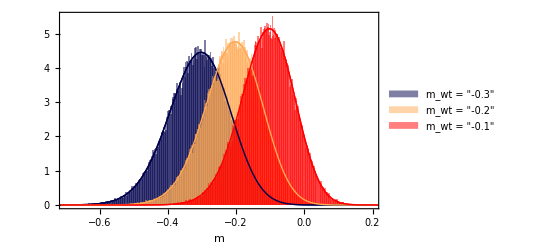

```mathematica
n=4;η=n/2;(*phenotypic dimensions*)
Es=0.01;(*mean mutational selective efffect*)
λ=2Es/n;(*mutational variance per trait*)

mmax=0.5; (*max growth rate*)
mwts={-0.3,-0.2,-0.1};nmwts=Length[mwts];(*scaled*)
zis=Table[√(2(mmax-mwts[[i]]))UnitVector[n,1],{i,nmwts}];(*vector from wildtype from the optimum along trait 1 axis*)

color={Darker[Blue,0.7],Lighter[Orange],Red};(*colors*)
styl={FontFamily-> "Times",FontSize->10};(*styles of axes and legend*)

legends=Table[StringForm["m_wt = ``",NumberForm[mwts[[i]],3]],{i,nmwts}]; simuls=Histogram[Table[mwts[[i]]+ss[dz,zis[[i]]],{i,nmwts}],500,"PDF",ChartStyle->color,PlotRange->{{-2,0.5},All},Axes->False,ChartLegends->Placed[legends,{0.2,0.8}]]; (*simulation results*)

Table[fm[m,mwts[[i]],mmax,λ,n],{i,nmwts}];
theory=Plot[%,{m,-1,0.5},PlotRange->{{-0.7,0.2},All},PlotStyle->color,Frame->{True,True,False,False},FrameLabel->{"m"}];

Show[{theory,simuls,theory},LabelStyle->styl,AxesLabel->{,"f(m | m_wt)"}]
(*Export[imagedir<>"fmmwt.pdf",%];*)

Clear[λ,n,mmax]
```

Approximation from Martin & Lenormand 2006 Evol 60:893:

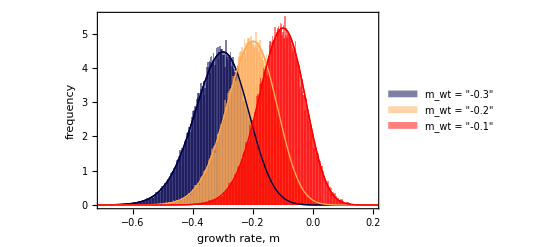

```mathematica
n=4;η=n/2;(*phenotypic dimensions*)
Es=0.01;(*mean mutational selective efffect*)
λ=2Es/n;(*mutational variance per trait*)

mmax=0.5; (*max growth rate*)
mwts={-0.3,-0.2,-0.1};nmwts=Length[mwts];(*scaled*)
zis=Table[√(2(mmax-mwts[[i]]))UnitVector[n,1],{i,nmwts}];(*vector from wildtype from the optimum along trait 1 axis*)

color={Darker[Blue,0.7],Lighter[Orange],Red};(*colors*)
styl={FontFamily-> "Times",FontSize->14};(*styles of axes and legend*)

legends=Table[Style[StringForm["m_wt = ``",NumberForm[mwts[[i]],3]],14],{i,nmwts}]; simuls=Histogram[Table[mwts[[i]]+ss[dz,zis[[i]]],{i,nmwts}],500,"PDF",ChartStyle->color,PlotRange->{{-2,0.5},All},Axes->False,ChartLegends->Placed[legends,{0.2,0.8}]]; (*simulation results*)

Table[Simplify[PDF[TransformedDistribution[so-γ,γ\[Distributed]GammaDistribution[β,α]],s],so-s>0]/.α->λ (1+2ϵ)/(1+ϵ)/.β->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.λ->2Es/n/.so->mmax-mwts[[i]]/.s->m-mwts[[i]],{i,nmwts}];
theory=Plot[%,{m,-1,0.5},PlotRange->{{-0.7,0.2},All},PlotStyle->color,Frame->{True,True,False,False},FrameLabel->{"growth rate, m","frequency"}];

Show[{theory,simuls,theory},LabelStyle->styl(*,AxesLabel->{,"f(m | m_wt)"}*)]
(*Export[imagedir<>"fmmwtApprox.pdf",%];*)

Clear[λ,n,mmax]
```

The distribution of potential rescue mutants (fluctuation test prediction)

{2.57725×10^43 ⅇ^(100.621 (-0.5+m)) (0.5-m)^80.5031,1.6471×10^42 ⅇ^(100.709 (-0.5+m)) (0.5-m)^70.5035,2.56319×10^40 ⅇ^(100.826 (-0.5+m)) (0.5-m)^60.5041}

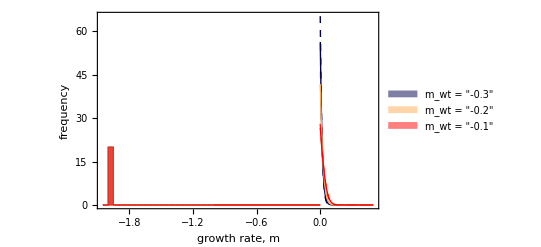

```mathematica
n=4;η=n/2;(*phenotypic dimensions*)
Es=0.01;(*mean mutational selective efffect*)
λ=2Es/n;(*mutational variance per trait*)

mmax=0.5; (*max growth rate*)
mwts={-0.3,-0.2,-0.1};nmwts=Length[mwts];(*scaled*)

color={Darker[Blue,0.7],Lighter[Orange],Red};(*colors*)
colordashed={Directive[Dashed,Darker[Blue,0.7]],Directive[Dashed,Lighter[Orange]],Directive[Dashed,Red]};(*colors*)
styl={FontFamily-> "Times",FontSize->14};(*styles of axes and legend*)

legends=Table[Style[StringForm["m_wt = ``",NumberForm[mwts[[i]],3]],14],{i,nmwts}];

Table[fm[m,mwts[[i]],mmax,λ,n],{i,nmwts}];
% 1 HeavisideTheta[m];
%/NIntegrate[%,{m,0,mmax}];
theory=Plot[%,{m,-1,0.5},PlotRange->{{-0.7,0.2},All},PlotStyle->color,Frame->{True,True,False,False},FrameLabel->{"m"}];
Table[Simplify[PDF[TransformedDistribution[so-γ,γ\[Distributed]GammaDistribution[β,α]],s],so-s>0]/.α->λ (1+2ϵ)/(1+ϵ)/.β->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.λ->2Es/n/.so->mmax-mwts[[i]]/.s->m-mwts[[i]],{i,nmwts}](*new mutations*)
% 1 HeavisideTheta[m];
%/NIntegrate[%,{m,0,mmax}];

approx=Plot[%,{m,0,mmax},PlotRange->{{0,mmax},All},PlotStyle->colordashed,Frame->{True,True,False,False},FrameLabel->{"growth rate, m","frequency"}];

simuls=Histogram[Table[{-1,-2},{i,nmwts}],20,"PDF",ChartStyle->color,PlotRange->{{-2,0.5},All},Axes->False,ChartLegends->Placed[legends,{0.8,0.8}]]; (*simulation results*)

Show[{approx,theory,simuls},LabelStyle->styl(*,AxesLabel->{,"f(m | m_wt)"}*),PlotRange->{{0,0.1},{0,All}}]
(*Export[imagedir<>"LuriaDFE.pdf",%];*)

Clear[λ,n,mmax,Es]
```

## Wildtype dynamics

Consider a wildtype with non-overlapping generations (discrete time), where the number of offspring per individual is Poisson distributed with rate e^m_wt. We are concerned with the case where the wildtype is declining, that is, with m_wt<0. Starting with n0 individuals in generation t=0, the expected number of individuals in generation t is

(ⅇ^mwt)^t n0

(1+mwt)^t n0

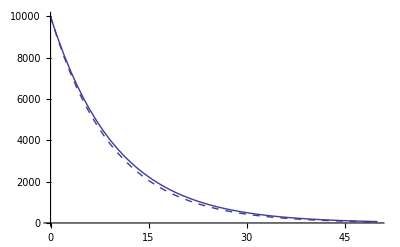

```mathematica
Clear[n]
nt=n[t]/.RSolve[{n[t+1]==Exp[mwt]n[t],n[0]==n0},n[t],t][[1]]
ntapp=n[t]/.RSolve[{n[t+1]==Normal[Series[Exp[mwt]n[t],{mwt,0,1}]],n[0]==n0},n[t],t][[1]]

Show[
Plot[nt/.n0->10^4/.mwt->-0.1,{t,0,50},PlotRange->{0,All}],
Plot[ntapp/.n0->10^4/.mwt->-0.1,{t,0,50},PlotStyle->Dashed,PlotRange->{0,All}],
PlotRange->{0,All}
]
```

The expected total number of wildtype individuals, nT, that exist before the demise of the wildtype is:

```mathematica
nT=Simplify[Sum[nt,{t,0,∞}],{mwt<0}]
Series[nT,{mwt,0,-1}]//Normal
```

-n0/(-1+ⅇ^mwt)

-n0/mwt

Each wildtype mutates with probability U and each of these lineages successfully rescues with probability p. Hence the probability generating function for the number of rescues is

```mathematica
Expectation[z^x,x\[Distributed]PoissonDistribution[nT U p]]
```

ⅇ^(-(n0 p U (-1+z))/(-1+ⅇ^mwt))

The probability of at least one rescue event is then

```mathematica
prescue=1-Expectation[z^x,x\[Distributed]PoissonDistribution[nT U p]]/.z->0
```

1-ⅇ^((n0 p U)/(-1+ⅇ^mwt))

## Mutant lineage dynamics

Here we use a continuous time birth (λ) death (μ) process to approximate the dynamics of our discrete time Poisson process (nonoverlapping generations with expected offspring exp(m)). To align these two approaches we need m = λ - μ and, as discussed in Uecker & Hermisson 2016 Genetics and Uecker et al 2014 Am Nat, λ + μ = 1. The latter requirement ensures both processes have the same amount of drift. We follow these studies in equally distributing m between λ and μ, such that λ = (1 + m)/2 and μ = (1 - m)/2. Note that this is only valid for |m|<1.

### The probability generating function

For a continuous-time birth death process starting from N0 individuals (F[s,0]==s^N0) the PGF for the number of individuals at time t can be solved for explicitly

```mathematica
fst=DSolve[{D[F[s,t],t]==D[F[s,t],s](λ s^2-(λ+μ)s+μ),F[s,0]==s^N0},F[s,t],{s,t}]//Flatten
```

{F[s,t]→((ⅇ^((μ (t λ-t μ+Log[-1+s]-Log[s λ-μ]))/(λ-μ))-ⅇ^((λ (t λ-t μ+Log[-1+s]-Log[s λ-μ]))/(λ-μ)) μ)/(ⅇ^((μ (t λ-t μ+Log[-1+s]-Log[s λ-μ]))/(λ-μ))-ⅇ^((λ (t λ-t μ+Log[-1+s]-Log[s λ-μ]))/(λ-μ)) λ))^N0}

### Persistence times

The probability of extinction at time t can be obtained from the PGF

```mathematica
pextt=F[s,t]/.fst/.s->0//Factor//FullSimplify
```

(1+(-λ+μ)/(λ-ⅇ^(t (-λ+μ)) μ))^N0

Evaluating at s=0 as t goes to infinity gives the probabilty the lineage ever goes extinct. When birth rate is greater than death rate, λ>μ ie m>0, we have

```mathematica
pextinction=Limit[F[s,t]/.fst/.s->0,t->∞,Assumptions->{λ>μ,μ>0}]
1-%/.λ->(1+m)/2/.μ->(1-m)/2/.N0->1;
Series[%,{m,0,1}]
```

(μ/λ)^N0

2 m+O[m]^2

(giving Haldane’s classic 2m approximation for the probability of establishment)

and when death rate is greater than birth rate we have

```mathematica
Limit[F[s,t]/.fst/.s->0,t->∞,Assumptions->{λ<μ,μ>0}]
```

1

The probability of persistence to time t is just one minus the probability of extinction by time t

```mathematica
pest=1-pextt
```

1-(1+(-λ+μ)/(λ-ⅇ^(t (-λ+μ)) μ))^N0

When |m| << 1/t << 1, ie |1/m| >> t >> 1 (that is, at late times but while the mutant is still effectively critical) the probability that a new mutant persists to time t is approximately

```mathematica
pestapp1=Normal[Series[pest/.λ->(1+m)/2/.μ->(1-m)/2/.N0->1/.m ->m ϵ^2/.t->t /ϵ,{ϵ,0,1}]]/.ϵ->1
```

2/t

And when -m t >>1, ie -m >> 1/t (that is, when the mutant is effectively subcritical) we have roughly

```mathematica
pestapp2=Simplify[pest/.λ->(1+m)/2/.μ->(1-m)/2/.N0->1]/. 1+ⅇ^(-m t) (-1+m)+m->ⅇ^(-m t) (-1+m)/.-1+m->-1
```

-2 ⅇ^(m t) m

Visually check the critical (red) and subcritical (green) approximations of the true solution (blue)

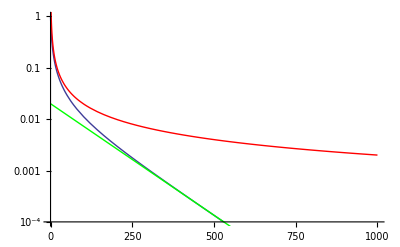

```mathematica
Show[
LogPlot[pest/.λ->(1+m)/2/.μ->(1-m)/2/.N0->1/.m->-0.01,{t,0,1000},PlotRange->{10^-4,1}],
LogPlot[pestapp1/.m->-0.01,{t,0,1000},PlotRange->All,PlotStyle->Red],
LogPlot[pestapp2/.m->-0.01,{t,0,1000},PlotRange->All,PlotStyle->Green]
]
```

Our equations for persistence times line-up with Weissman et al 2010 Genetics eq A2, but with an additional factor of 2 because of our birth-death model (they assume binary fission). They point out that the distribution of persistence time has a long tail (like 1/t) before falling off exponentially when t > -1 / m (as can be seen in the plot above). Thus we can essentially say that a mutant lineage will not persist past t = -1 / m.

### Distribution of lineage sizes

The probability that there is 1 individual at time t is

```mathematica
pn1=D[F[s,t]/.fst,{s,n}]/n!/.n->1/.s->0/.λ->(1+m)/2/.μ->(1-m)/2/.N0->1//Simplify
```

(4 ⅇ^(m t) m^2)/((-1+m+ⅇ^(m t) (1+m))^2)

and two individuals

```mathematica
pn2=D[F[s,t]/.fst,{s,n}]/n!/.n->2/.s->0/.λ->(1+m)/2/.μ->(1-m)/2/.N0->1//Simplify
```

(4 ⅇ^(m t) (-1+ⅇ^(m t)) m^2 (1+m))/((-1+m+ⅇ^(m t) (1+m))^3)

three

```mathematica
D[F[s,t]/.fst,{s,n}]/n!/.n->3/.s->0/.λ->(1+m)/2/.μ->(1-m)/2/.N0->1//Simplify
```

(4 ⅇ^(m t) (-1+ⅇ^(m t))^2 m^2 (1+m)^2)/((-1+m+ⅇ^(m t) (1+m))^4)

From this series we can see that we can write the probability of n individuals at time t like

```mathematica
pnt=pn1(pn2/pn1)^(n-1)
```

(4 ⅇ^(m t) m^2 (((-1+ⅇ^(m t)) (1+m))/(-1+m+ⅇ^(m t) (1+m)))^(-1+n))/((-1+m+ⅇ^(m t) (1+m))^2)

Check for n=4:

```mathematica
pnt/(D[F[s,t]/.fst,{s,n}]/n!)/.n->4/.s->0/.λ->(1+m)/2/.μ->(1-m)/2/.N0->1//Simplify
```

1

### Distribution of lineage sizes given persistence

Dividing the probability of having n individuals at time t by the probability of survival to time t gives the conditional probability of having n individuals at time t given a mutant lineage lives to time t

```mathematica
pntgt=pnt/pest/.λ->(1+m)/2/.μ->(1-m)/2/.N0->1//FullSimplify
```

(2 m (1-(2 m)/(-1+m+ⅇ^(m t) (1+m)))^n)/((-1+ⅇ^(m t)) (1+m))

When t << |1/m|  (effectively critical) this is approximately

```mathematica
pntgtapp1=Normal[Series[pntgt/.m-> m ϵ,{ϵ,0,0}]]/.ϵ->1//FullSimplify
Simplify[%==2 (1/t)(1+2/t)^-n,{t>0,n>0}]
```

2 t^(-1+n) (2+t)^-n

True

which for large t (requiring very critical mutants) is approximately

```mathematica
2 t^(-1+n) (2+t)^-n/. 2+t->t
```

2/t

Or when -1/m << t (ie subcritical mutants) we have approximately

```mathematica
pntgtapp2=pntgt/.-1+m+ⅇ^(m t) (1+m)->-1+m/.-1+ⅇ^(m t)->-1//Simplify;
%/. 1-m->1
```

-2 m (1+m)^(-1+n)

Visually check critical (red) and subcritical (green) approximations against true solution (blue)

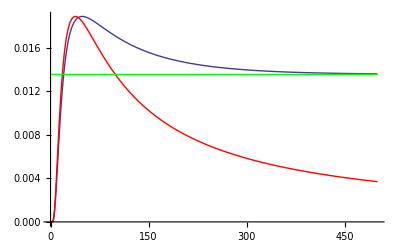

```mathematica
Show[
Plot[pntgt/.m->-0.01/.n->20,{t,0,500},PlotRange->All],
Plot[pntgtapp1/.m->-0.01/.n->20,{t,0,500},PlotRange->All,PlotStyle->Red],
Plot[pntgtapp2/.m->-0.01/.n->20,{t,0,500},PlotRange->All,PlotStyle->Green]
]
```

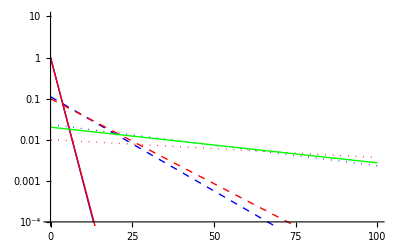

```mathematica
nmax=100;
Show[
LogPlot[pntgt/.m->-0.01/.t->2,{n,0,nmax},PlotStyle->Blue,PlotRange->{10^-4,10}],
LogPlot[pntgt/.m->-0.01/.t->20,{n,0,nmax},PlotStyle->{Blue,Dashed},PlotRange->All],
LogPlot[pntgt/.m->-0.01/.t->200,{n,0,nmax},PlotStyle->{Blue,Dotted,Thick},PlotRange->All],
LogPlot[pntgtapp1/.m->-0.01/.t->2,{n,0,nmax},PlotRange->All,PlotStyle->Red],
LogPlot[pntgtapp1/.m->-0.01/.t->20,{n,0,nmax},PlotRange->All,PlotStyle->{Red,Dashed}],
LogPlot[pntgtapp1/.m->-0.01/.t->200,{n,0,nmax},PlotRange->All,PlotStyle->{Red,Dotted,Thick}],
LogPlot[pntgtapp2/.m->-0.01,{n,0,nmax},PlotRange->All,PlotStyle->Green]
]
```

These lineage sizes given persistence align with eq A3 in Weissman et al 2010. As they pointed out, the distribution of n given persistence to t and m is roughly geometric in both cases (t<<|1/m| and t>>-1/m), with p=1/t or p=-m respectively, which implies that the probability of n drops off exponentially when n>min(t, -1/m). Thus n will essentially never be greater than the minimum of t or -1/m, eg mutants with large -m will be restricted to small sizes.

## Probability of establishment

Here we derive the probability a mutant with growth rate m establishes. We use the Feller diffusion approximation (see Martin et al 2013 Phil Trans B sup mat for details). The probability of establishment is then

```mathematica
1-Exp[-2r/σ]
```

1-ⅇ^(-(2 r)/σ)

where r is the infinitesimal mean and σ is the infinitesimal variance in growth rate.

In our discrete generation Poisson process, r is

```mathematica
Expectation[X-1,X\[Distributed]PoissonDistribution[Exp[m]]]
```

-1+ⅇ^m

and σ is

```mathematica
Expectation[(X-1)^2,X\[Distributed]PoissonDistribution[Exp[m]]]-Expectation[X-1,X\[Distributed]PoissonDistribution[Exp[m]]]^2//Simplify//Simplify
```

ⅇ^m

When m is small these are roughly

```mathematica
Series[Exp[m]-1,{m,0,1}]//Normal
```

m

and

```mathematica
Series[Exp[m],{m,0,0}]//Normal
```

1

Then the probability of establishment for m>0 is

```mathematica
1-Exp[-2r/σ]/.r->m/.σ->1
```

1-ⅇ^(-2 m)

or 0 when r<0.

Note that this reduces to both Haldane’s (1927 Mathematical Proceedings of the Cambridge Philosophical Society) constant population size result and Otto & Whitlock’s (1997 Genetics) changing population size result when m is small

```mathematica
Normal[Series[1-ⅇ^(-2 m),{m,0,1}]]/.m->Subscript[m, wt]+s/.Subscript[m, wt]->0
```

2 s

```mathematica
Normal[Series[1-ⅇ^(-2 m),{m,0,1}]]/.m->Subscript[m, wt]+s
```

2 (s+m_wt)

## The problem(s)

We want to know the probability a mutant lineage is successful at rescuing the population, p. We will break this up into the following sub-problems:

(a) What is the probability that any of the X mutations is directly successful? (1-step rescue)

(b) What is the probability that any of the X mutations is not directly successful but produces a mutant lineage which is? (2-step rescue)

We address each in turn.

## (a) 1-step rescue

(a) What is the probability that at least one single mutant lineage is directly successful?

### Probability of rescue

We can get the probability a single mutant arises and establishes by numerically integrating P_est(m) f(m) over m from 0 to mmax. This then gives us the probability of 1-step rescue

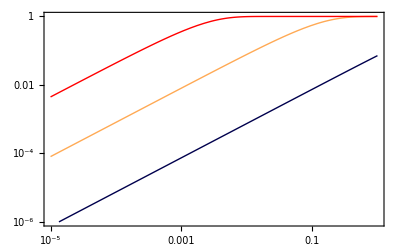

```mathematica
n=4;η=n/2;(*phenotypic dimensions*)
Es=0.01;(*mean mutational selective efffect*)
λ=2Es/n;(*mutational variance per trait*)
n0=10^4;

mmax=0.5; (*max growth rate*)
mwts={-0.3,-0.2,-0.1};nmwts=Length[mwts];(*wildtype growth rates*)
color={Darker[Blue,0.7],Lighter[Orange],Red};(*colors*)

Table[prescue/.mwt->mwts[[i]]/.p->NIntegrate[(1-Exp[-2m])fm[m,mwts[[i]],mmax,λ,n],{m,0,mmax}],{i,nmwts}];
feller=LogLogPlot[%,{U,10^-5,10^0},PlotStyle->color,Frame->{True,True,False,False},PlotRange->{10^-6,1}];

Show[feller]

Clear[λ,n,mmax,Es,n0]
```

We can’t integrate this over m analytically. Lets instead use the approximation from Martin & Lenormand 2006 Evol 60:893. We can integrate this approximation

```mathematica
Simplify[PDF[TransformedDistribution[so-γ,γ\[Distributed]GammaDistribution[β,α]],s],so-s>0]/.so->mmax-mwt/.s->m-mwt;
P1stepApp=Integrate[(1-Exp[-2m]) %,{m,0,mmax},Assumptions->{mmax>0,β>0,α>0}]
```

1+(ⅇ^(-2 mmax) (1-2 α)^-β (-Gamma[β]+Gamma[β,mmax (-2+1/α)]))/Gamma[β]-Gamma[β,mmax/α]/Gamma[β]

Check that the probability of rescue is a good approximation

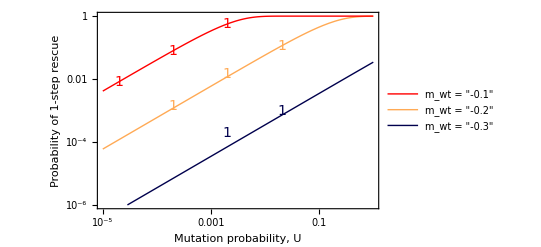

```mathematica
Clear[mmax,n,λ,Es]
mmax=0.5;
Es=0.01;
λ=2Es/n;
n=4;
n0=10^4;
mwts={-0.3,-0.2,-0.1};nmwts=Length[mwts];
color={Darker[Blue,0.7],Lighter[Orange],Red};(*colors*)
colorthick={Directive[Thick,Darker[Blue,0.7]],Directive[Thick,Lighter[Orange]],Directive[Thick,Red]};(*colors*)
styl={FontFamily-> "Times",FontSize->14};(*styles of axes and legend*)
legends=Table[Style[StringForm["m_wt = ``",NumberForm[mwts[[i]],3]],14],{i,nmwts}]; 

P1stepApp/.α->λ (1+2ϵ)/(1+ϵ)/.β->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax-mwt;
Table[prescue/.p->%/.mwt->mwts[[i]],{i,nmwts}];
feller=LogLogPlot[%,{U,10^-5,1},PlotStyle->colorthick,PlotRange->{10^-6,1}];

Import[datadir<>"prescue_poisson_N10000_n4_Es0.01_mmax0.50_mwt-0.30_nreps10000.csv"];
dat=Table[Select[%,#[[2]]==i&][[All,{1,3}]],{i,{1(*,2,10*)}}];
dat[[All,All,{1}]]=dat[[All,All,{1}]]*Uc/.Uc->n^2 λ/4;
data1=ListLogLogPlot[dat,PlotMarkers->{Style["1",14],"2","10"},PlotStyle->{{color[[1]],PointSize[Large]},{color[[1]],PointSize[Large]},{color[[1]],PointSize[Large]}}];

Import[datadir<>"prescue_poisson_N10000_n4_Es0.01_mmax0.50_mwt-0.20_nreps10000.csv"];
dat=Table[Select[%,#[[2]]==i&][[All,{1,3}]],{i,{1(*,2,10*)}}];
dat[[All,All,{1}]]=dat[[All,All,{1}]]*Uc/.Uc->n^2 λ/4;
data2=ListLogLogPlot[dat,PlotMarkers->{Style["1",14],"2","10"},PlotStyle->{{color[[2]],PointSize[Large]},{color[[2]],PointSize[Large]},{color[[2]],PointSize[Large]}}];

Import[datadir<>"prescue_poisson_N10000_n4_Es0.01_mmax0.50_mwt-0.10_nreps10000.csv"];
dat=Table[Select[%,#[[2]]==i&][[All,{1,3}]],{i,{1(*,2,10*)}}];
dat[[All,All,{1}]]=dat[[All,All,{1}]]*Uc/.Uc->n^2 λ/4;
data3=ListLogLogPlot[dat,PlotMarkers->{Style["1",14],"2","10"},PlotStyle->{{color[[3]],PointSize[Large]},{color[[3]],PointSize[Large]},{color[[3]],PointSize[Large]}}];

Legended[
Show[(*full,*)feller,data1,data2,data3,
Frame->{True,True,False,False},
FrameLabel->{"Mutation probability, U","Probability of 1-step rescue"},
LabelStyle->styl
],
Placed[
LineLegend[Reverse[colorthick],Reverse[legends]],
Scaled@{0.8,0.25}
]
]

(*Export[imagedir<>"P1step.pdf",%];
*)
Clear[mmax,n,λ,Es,n0]
```

### Comparison with Anciaux et al 2018 Genetics

Let’s first convert the exact pdf of mutant growth rates to their variables and check that this integrates to 1:

```mathematica
FullSimplify[Simplify[ρmax λ fm[m,mwt,mmax,λ,n],{mmax>m,λ>0}]/.mwt->-yD mmax/.m->y mmax/.mmax->λ ρmax/.n->2θ,{θ>0,ρmax>0,0<y<1}]
NIntegrate[%/.λ->0.02/.ρmax->10/.θ->5/.yD->0.1,{y,-∞,1}]
```

-(ⅇ^((-2+y-yD) ρmax) (ρmax-y ρmax)^θ Hypergeometric0F1Regularized[θ,-(-1+y) (1+yD) ρmax^2])/(-1+y)

1.

Note that we have to multiply f(m) by ρmax λ to get a proper pdf (integrates to 1) because we have rescaled the x-axis in our switch from m to y.

They then take the limit as ρmax = mmax/λ goes to infinity (that is, as the distance to the optimum becomes much greater than the variance in mutational effects). We have instead used the approximation in Martin & Lenormand 2006, which assumes that s ~ m - mwt is small (which is also a small mutation assumption).

Compare our approximate pdf of scaled mutant growth with theirs (eq A9) and the full solution

1.

1.00134

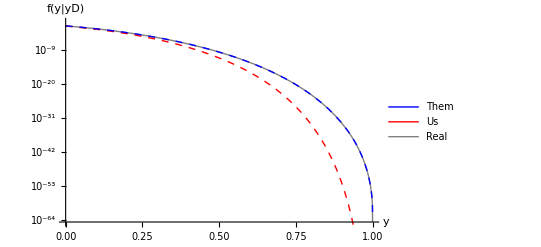

```mathematica
vars={ρmax->mmax/λ,θ->n/2,yD->-mwt/mmax,λ->2Es/n};
params={mmax->0.5,mwt->-0.2,Es->0.01,n->4};

(*our approx*)
Simplify[PDF[TransformedDistribution[so-γ,γ\[Distributed]GammaDistribution[β,α]],s],so-s>0]/.so->mmax-mwt/.s->m-mwt/.α->λ (1+2ϵ)/(1+ϵ)/.β->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax-mwt;
λ ρmax%/.mwt->-yD mmax/.m->y mmax/.mmax->λ ρmax/.n->2θ//Simplify;
us=LogPlot[%/.vars/.vars/.params,{y,0,0.99},PlotStyle->{Thick,Red,Dashed},PlotRange->{0,All}];
NIntegrate[%%/.vars/.vars/.params,{y,-∞,1}]

(*their approx*)
(√ρmax)/(2 √π)(1+yD)^(1/4-θ/2)Exp[-vy](1-y)^(θ/2-3/4);
%/.vy->ρmax(2+yD-2 √((1+yD)(1-y))-y);
them=LogPlot[%/.vars/.vars/.params,{y,0,1},PlotRange->{0,All},PlotStyle->{Thick,Blue,Dashed}];
NIntegrate[%%/.vars/.vars/.params,{y,-∞,1}]

(*full solution*)
ρmax λ fm[m,mwt,mmax,λ,n]/.mwt->-yD mmax/.m->y mmax/.mmax->λ ρmax/.n->2θ;
%/.vars/.vars/.params;
real=LogPlot[%,{y,0,1},PlotRange->{0,All},PlotStyle->{Thick,Gray}];

Legended[
Show[real,us,them,
AxesLabel->{"y","f(y|yD)"}],
Placed[
LineLegend[{Blue,Red,Gray},{"Them", "Us", "Real"}],
Scaled@{0.25,0.25}
]
]
```

Their approximation is better, but ours is good where most of the weight is (on the left; note the log scale).

Finally, let’s compare the per capita rate of rescue (their eq 7a):

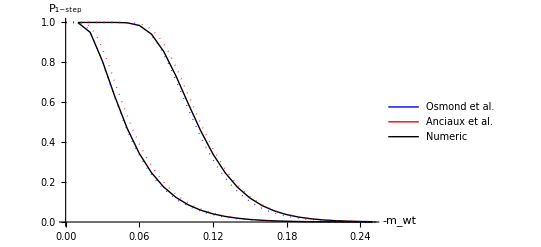

{0.0002,0.00002}

```mathematica
Es=0.01;
n=4;
n0=10^5;
U=x Uc;
Uc=n^2 λ/4;

mmax=0.5;
vars={ρmax->mmax/λ,θ->n/2,yD->-mwt/mmax,λ->2Es/n};
us=(U n0)/(1-Exp[mwt])(1+(ⅇ^(-2 mmax) (1-2 α)^-β (-Gamma[β]+Gamma[β,mmax (-2+1/α)]))/Gamma[β]-Gamma[β,mmax/α]/Gamma[β])/.α->λ (1+2ϵ)/(1+ϵ)/.β->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax-mwt/.mwt->-yD mmax/.m->y mmax/.mmax->λ ρmax/.n->2θ/.vars/.vars/.mwt->-rD;

them=n0 U(1+ψD/2)^(1/2-θ)/(1+ψD/4)g[α]/.g[α]->Exp[-α]/(√(π α))-Erfc[√α]/.α->ψD^2 ρmax/4/.ψD->2(√(1+yD)-1)/.vars/.vars/.mwt->-rD;

(n0 U)/(1-Exp[mwt])(1-Exp[-2m])ρmax λ fm[m,mwt,mmax,λ,n]/.mwt->-yD mmax/.m->y mmax/.mmax->λ ρmax/.n->2θ;
%/.vars/.vars/.mwt->-rD;
Table[{rD,1-Exp[-NIntegrate[%,{y,0,1}]]},{x,{10^-2,10^-3}},{rD,0.01,0.25,0.01}];
real=ListPlot[%,Joined->True,PlotStyle->{{Black,Thick},{Black,Thick}}];

pltA=Legended[
Show[
real,
Plot[1-Exp[-(us)]/.x->{10^-2,10^-3},{rD,0,0.45},PlotRange->{0,1.1},PlotStyle->{Blue,Dotted,Thick}],
Plot[1-Exp[-(them)]/.x->{10^-2,10^-3},{rD,0,0.45},PlotRange->{0,1.1},PlotStyle->{Red,Dotted,Thick}],
AxesLabel->{Style["-m_wt",16],Style["P_(1-step)",16]},
AxesStyle->Directive[FontSize->16]
],
Placed[
LineLegend[{Directive[Thick,Blue],Directive[Thick,Red],Directive[Thick,Black]},{Style["Osmond et al.",16],Style["Anciaux et al.",16],Style["Numeric",16]}],
Scaled@{0.8,0.8}
]
]

Export[imagedir<>"AnciauxComparison.pdf",%];

U/.λ->2Es/n/.x->{10^-2,10^-3}
(*mmax=1.5;
vars={ρmax->mmax/λ,θ->n/2,yD->-mwt/mmax,λ->2Es/n};

us=-(U n0)/mwt(1+(ⅇ^(-2 mmax) (1-2 α)^-β (-Gamma[β]+Gamma[β,mmax (-2+1/α)]))/Gamma[β]-Gamma[β,mmax/α]/Gamma[β])/.α->λ (1+2ϵ)/(1+ϵ)/.β->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax-mwt/.mwt->-yD mmax/.m->y mmax/.mmax->λ ρmax/.n->2θ/.vars/.vars/.mwt->-rD;

them=n0 U(1+ψD/2)^(1/2-θ)/(1+ψD/4)g[α]/.g[α]->Exp[-α]/(√(π α))-Erfc[√α]/.α->ψD^2 ρmax/4/.ψD->2(√(1+yD)-1)/.vars/.vars/.mwt->-rD;

pltB=Show[
Plot[1-Exp[-(us)]/.x->{10^-2,10^-3},{rD,0,0.45},PlotRange->{0,1.1},PlotStyle->{Blue,Dashed,Thick}],
Plot[1-Exp[-(them)]/.x->{10^-2,10^-3},{rD,0,0.45},PlotRange->{0,1.1},PlotStyle->{Red,Dashed,Thick}],
AxesLabel->{"r_D","P_R"}
];

GraphicsColumn[{pltA,pltB}]*)

Clear[Es,mmax,n,n0,U,Uc,B]
```

This is Anciaux et al 2018 figure 2A, and our approximations are just slight underestimates of theirs. Note that they show that their approximation works very well compared to simulations (in fact they overestimate slightly).

#### clean-up below here, update code

Let’s first check that our simulations are working by using the same parameters as Anciaux et al 2018 Figure 2 (but let’s stick with a log scale for the probability of rescue and with growth rates rather than decline rates; and just the orange U=10^-2 Uc results):

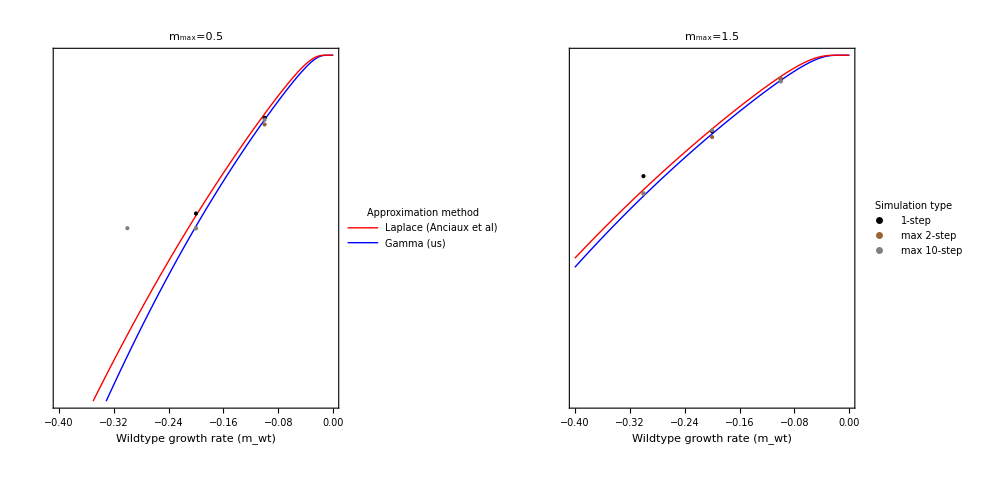

```mathematica
Es=0.01;
mmax=0.5;
n=4;
n0=10^4;
U=10^-2 Uc;
Uc=n^2 λ/4;
ymin=10^-6;
xmin=-0.4;

onesteprate=-(n0 U)/(1-Exp[Subscript[m, wt]]) (1+(ⅇ^(-2 mmax) (1-2 α)^-β (-Gamma[β]+Gamma[β,mmax (-2+1/α)]))/Gamma[β]-Gamma[β,mmax/α]/Gamma[β])/.α->λ (1+2ϵ)/(1+ϵ)/.β->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax-mwt/.Subscript[m, wt]->mwt/.λ->2Es/n;

vars={ρmax->mmax/λ,θ->n/2,yD->-mwt/mmax,λ->2Es/n};
anciaux=n0 U(1+ψD/2)^(1/2-θ)/(1+ψD/4)g[α]/.g[α]->Exp[-α]/(√(π α))-Erfc[√α]/.α->ψD^2 ρmax/4/.ψD->2(√(1+yD)-1)/.vars/.vars;

data1step=Import[datadir<>"prescue_poisson_N10000_n4_U0.00020_Es0.01_mmax0.50_mutmax1_nreps10000.csv"];
data2step=Import[datadir<>"prescue_poisson_N10000_n4_U0.00020_Es0.01_mmax0.50_mutmax2_nreps1000.csv"];
data10step=Import[datadir<>"prescue_poisson_N10000_n4_U0.00020_Es0.01_mmax0.50_mutmax10_nreps1000.csv"];

fig2A=
Legended[
Show[
LogPlot[1-Exp[-(onesteprate)],{mwt,xmin,0},PlotRange->{ymin,1},PlotStyle->Blue,FrameTicks->{{None,All},{All,None}}],
LogPlot[1-Exp[-(anciaux)],{mwt,xmin,0},PlotRange->{ymin,1},PlotStyle->Red],
ListLogPlot[data1step, PlotStyle->Directive[Black,PointSize->Large]],
ListLogPlot[data2step, PlotStyle->Directive[Brown,PointSize->Large]],
ListLogPlot[data10step, PlotStyle->Directive[Gray,PointSize->Large]],
Frame->{True,False,False,True},
FrameLabel->{Style["Wildtype growth rate (m_wt)",16],,,Style["Probability of rescue",16]},
FrameTicksStyle->12,
PlotLabel->Style["m_max=0.5",Bold]
],
Placed[
LineLegend[{Red,Blue},{ "Laplace (Anciaux et al)","Gamma (us)"},LegendLabel->Style["Approximation method",Bold]],
Scaled@{0.25,0.75}
]
];

mmax=1.5;

onesteprate=-(n0 U)/Subscript[m, wt] (1+(ⅇ^(-2 mmax) (1-2 α)^-β (-Gamma[β]+Gamma[β,mmax (-2+1/α)]))/Gamma[β]-Gamma[β,mmax/α]/Gamma[β])/.α->λ (1+2ϵ)/(1+ϵ)/.β->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax-mwt/.Subscript[m, wt]->mwt/.λ->2Es/n;

vars={ρmax->mmax/λ,θ->n/2,yD->-mwt/mmax,λ->2Es/n};
anciaux=n0 U(1+ψD/2)^(1/2-θ)/(1+ψD/4)g[α]/.g[α]->Exp[-α]/(√(π α))-Erfc[√α]/.α->ψD^2 ρmax/4/.ψD->2(√(1+yD)-1)/.vars/.vars;

data1step=Import[datadir<>"prescue_poisson_N10000_n4_U0.00020_Es0.01_mmax1.50_mutmax1_nreps1000.csv"];
data2step=Import[datadir<>"prescue_poisson_N10000_n4_U0.00020_Es0.01_mmax1.50_mutmax2_nreps1000.csv"];
data10step=Import[datadir<>"prescue_poisson_N10000_n4_U0.00020_Es0.01_mmax1.50_mutmax10_nreps1000.csv"];

fig2B=
Legended[
Show[
LogPlot[1-Exp[-(onesteprate)],{mwt,xmin,0},PlotRange->{ymin,1},PlotStyle->Blue,FrameTicks->{{None,All},{All,None}}],
LogPlot[1-Exp[-(anciaux)],{mwt,xmin,0},PlotRange->{ymin,1},PlotStyle->Red],
ListLogPlot[data1step, PlotStyle->Directive[Black,PointSize->Large]],
ListLogPlot[data2step, PlotStyle->Directive[Brown,PointSize->Large]],
ListLogPlot[data10step, PlotStyle->Directive[Gray,PointSize->Large]],
Frame->{True,False,False,True},
FrameLabel->{Style["Wildtype growth rate (m_wt)",16],,,Style["Probability of rescue",16]},
FrameTicksStyle->12,
PlotLabel->Style["m_max=1.5",Bold]
],
Placed[
PointLegend[{Directive[Black,PointSize->Large],Directive[Brown,PointSize->Large],Directive[Gray,PointSize->Large]},{"1-step","max 2-step","max 10-step"},LegendLabel->Style["Simulation type",Bold]],
Scaled@{0.75,0.25}
]
];

GraphicsRow[{fig2A,fig2B},ImageSize->1000,AspectRatio->1/GoldenRatio]

Clear[Es,mmax,n,n0,U,Uc,B,xmin,ymin]
```

Here we see that the probability of rescue is similar regardless of whether we allow a maximum of 1, 2, or 10 mutations per individual (there is a lot of stochasticity below 0.01 because we only ran 1000 replicates, this explains the gray dot on the far left of the left plot -- a single rescue event happened). This implies that rescue is primarily happening by one mutational step. We also see that our approximation (blue) matches Anciaux (red), and both do well relative to simulations (dots).

Lets see if we can break the 1-step assumption. Anciaux et al follow Martin & Roques 2016 (Genetics) by saying that we need U << Uc for the SSWM assumption to hold. This assumption, Strong Selection Weak Mutation, allows us to neglect individuals with multiple mutations, and hence means that 1-step rescue should dominate. If we set U=Uc then we should see that the 1-step rescue probability begins to fail and the 2-step rescue starts to play a role:

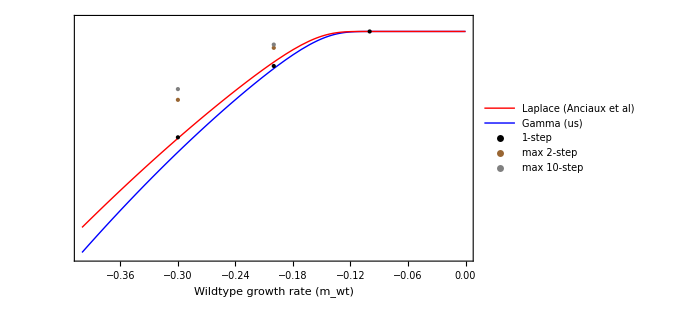

```mathematica
Es=0.01;
mmax=0.5;
n=4;
n0=10^4;
U=10^-0 Uc;
Uc=n^2 λ/4;
ymin=10^-6;
xmin=-0.4;

onesteprate=(n0 U)/(1-Exp[Subscript[m, wt]]) (1+(ⅇ^(-2 mmax) (1-2 α)^-β (-Gamma[β]+Gamma[β,mmax (-2+1/α)]))/Gamma[β]-Gamma[β,mmax/α]/Gamma[β])/.α->λ (1+2ϵ)/(1+ϵ)/.β->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax-mwt/.Subscript[m, wt]->mwt/.λ->2Es/n;

vars={ρmax->mmax/λ,θ->n/2,yD->-mwt/mmax,λ->2Es/n};
anciaux=n0 U(1+ψD/2)^(1/2-θ)/(1+ψD/4)g[α]/.g[α]->Exp[-α]/(√(π α))-Erfc[√α]/.α->ψD^2 ρmax/4/.ψD->2(√(1+yD)-1)/.vars/.vars;

data1step=Import[datadir<>"prescue_poisson_N10000_n4_U0.02000_Es0.01_mmax0.50_mutmax1_nreps10000.csv"];
data2step=Import[datadir<>"test_prescue_poisson_N10000_n4_U0.02000_Es0.01_mmax0.50_mutmax2_nreps1000.csv"];
data10step=Import[datadir<>"test_prescue_poisson_N10000_n4_U0.02000_Es0.01_mmax0.50_mutmax10_nreps1000.csv"];

Legended[
Show[
LogPlot[1-Exp[-(onesteprate)],{mwt,xmin,0},PlotRange->{ymin,2},PlotStyle->Blue,FrameTicks->{{None,All},{All,None}}],
LogPlot[1-Exp[-(anciaux)],{mwt,xmin,0},PlotRange->{ymin,1},PlotStyle->Red],
ListLogPlot[data1step, PlotStyle->Directive[Black,PointSize->Large]],
ListLogPlot[data2step, PlotStyle->Directive[Brown,PointSize->Large]],
ListLogPlot[data10step, PlotStyle->Directive[Gray,PointSize->Large]],
Frame->{True,False,False,True},
FrameLabel->{Style["Wildtype growth rate (m_wt)",16],,,Style["Probability of rescue",16]},
FrameTicksStyle->12,
(*PlotLabel->"m_max=0.5",*)
ImageSize->500,
AspectRatio->1/GoldenRatio
],
{
Placed[
LineLegend[{Red,Blue},{ "Laplace (Anciaux et al)","Gamma (us)"},LegendLabel->Style["Approximation method",Bold]],
Scaled@{0.75,0.25}
],
Placed[
PointLegend[{Directive[Black,PointSize->Large],Directive[Brown,PointSize->Large],Directive[Gray,PointSize->Large]},{"1-step","max 2-step","max 10-step"},LegendLabel->Style["Simulation type",Bold]],
Scaled@{0.75,0.6}
]
}
]

Clear[Es,mmax,n,n0,U,Uc,B,xmin,ymin]
```

Here we see that allowing 2-step rescue increases the probability of rescue (by an order of magnitude), but allowing 10-step doesn’t offer much more. Thus with U=Uc the 2-step path is the single biggest contributer.

I think it would be nice to delimate the mutation rates that allow 1-step, 2-step etc to be good approximations. to make a first pass at this we can plot the probability of rescue as a function of U

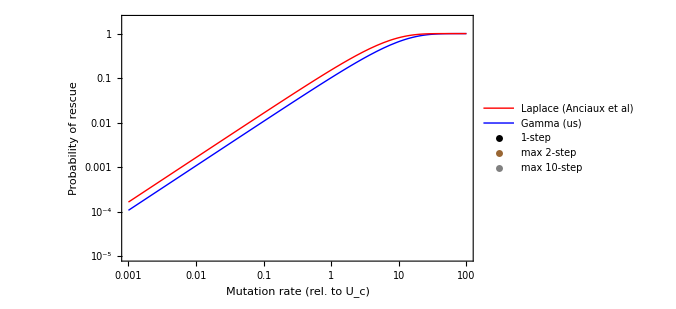

```mathematica
Es=0.01;
mmax=0.5;
n=4;
n0=10^4;
Uc=n^2 λ/4;
U=c Uc;
mwt=-0.2;
ymin=10^-5;
xmin=10^-3;
xmax=10^2;

onesteprate=-(n0 U)/Subscript[m, wt] (1+(ⅇ^(-2 mmax) (1-2 α)^-β (-Gamma[β]+Gamma[β,mmax (-2+1/α)]))/Gamma[β]-Gamma[β,mmax/α]/Gamma[β])/.α->λ (1+2ϵ)/(1+ϵ)/.β->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax-mwt/.Subscript[m, wt]->mwt/.λ->2Es/n;

vars={ρmax->mmax/λ,θ->n/2,yD->-mwt/mmax,λ->2Es/n};
anciaux=n0 U(1+ψD/2)^(1/2-θ)/(1+ψD/4)g[α]/.g[α]->Exp[-α]/(√(π α))-Erfc[√α]/.α->ψD^2 ρmax/4/.ψD->2(√(1+yD)-1)/.vars/.vars;

Legended[
Show[
LogLogPlot[1-Exp[-(onesteprate)],{c,xmin,xmax},PlotRange->{ymin,2},PlotStyle->Blue,FrameTicks->{{All,None},{All,None}}],
LogLogPlot[1-Exp[-(anciaux)],{c,xmin,xmax},PlotRange->{ymin,1},PlotStyle->Red],
Frame->{True,True,False,False},
FrameLabel->{Style["Mutation rate (rel. to U_c)",16],Style["Probability of rescue",16]},
FrameTicksStyle->12,
(*PlotLabel->"m_max=0.5",*)
ImageSize->500,
AspectRatio->1/GoldenRatio
],
{
Placed[
LineLegend[{Red,Blue},{ "Laplace (Anciaux et al)","Gamma (us)"},LegendLabel->Style["Approximation method",Bold]],
Scaled@{0.5,0.24}
],
Placed[
PointLegend[{Directive[Black,PointSize->Large],Directive[Brown,PointSize->Large],Directive[Gray,PointSize->Large]},{"1-step","max 2-step","max 10-step"},LegendLabel->Style["Simulation type",Bold]],
Scaled@{0.85,0.2}
]
}
]

Clear[Es,mmax,n,n0,U,Uc,B,xmin,ymin,xmax,mwt]
```

### Distribution of mutant growth rates given rescue

From Bayes theorem, f(m | rescue) = (f(m)P(rescue | m))/(P(rescue)) where f are probability density functions. We already know f(m) from Martin & Lenormand 2015. The probability that a mutant rescues the population is 0 if m<0 and if m>0,

```mathematica
Prescuem=1-Exp[-2m]
```

1-ⅇ^(-2 m)

The probability of rescue is this times f(m) integrated over all m>0, which we have already calculated

```mathematica
P1stepApp
```

1+(ⅇ^(-2 mmax) (1-2 α)^-β (-Gamma[β]+Gamma[β,mmax (-2+1/α)]))/Gamma[β]-Gamma[β,mmax/α]/Gamma[β]

We then have an approximation for the distribution of m given rescue

```mathematica
Simplify[PDF[TransformedDistribution[so-γ,γ\[Distributed]GammaDistribution[β,α]],s],so-s>0]/.so->mmax-mwt/.s->m-mwt;
PmrescueApprox=Simplify[(% Prescuem)/P1stepApp,{α>0,β>0,mmax>0}]
```

(ⅇ^((m-mmax)/α) (1-ⅇ^(-2 m)) (-m+mmax)^(-1+β) α^-β)/(Gamma[β] (1+(ⅇ^(-2 mmax) (1-2 α)^-β (-Gamma[β]+Gamma[β,mmax (-2+1/α)]))/Gamma[β]-Gamma[β,mmax/α]/Gamma[β]))

Of course this does not depend on n0 and U as we are conditioning on rescue occurring, but it does depend on mmax and so = mmax - mwt. i.e., it is just the pdf of fixed mutations.

The approximation does pretty well

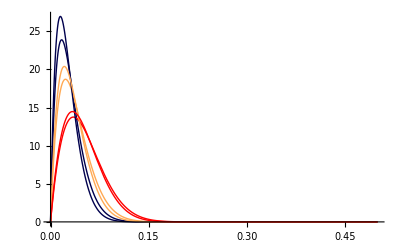

```mathematica
n=4;
Es=0.01;
λ=2Es/n;
mmax=0.5;
n0=10^4;
U=0.002;
mwts={-0.3,-0.2,-0.1};nmwts=Length[mwts];(*wildtype growth rates*)
color={Darker[Blue,0.7],Lighter[Orange],Red};(*colors*)
colordashed={{Dashed,Darker[Blue,0.7]},{Dashed,Lighter[Orange]},{Dashed,Red}};(*colors*)

Simplify[Table[(fm[m,mwt,mmax,λ,n]Prescuem)/NIntegrate[fm[m,mwt,mmax,λ,n]Prescuem/.mwt->mwts[[i]],{m,0,mmax}]/.mwt->mwts[[i]],{i,nmwts}],m<mmax];
realfull=Plot[%,{m,0,mmax},PlotStyle->color,PlotRange->All];

Table[PmrescueApprox/.α->λ (1+2ϵ)/(1+ϵ)/.β->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax-mwt/.mwt->mwts[[i]]//Simplify,{i,nmwts}];
bigapprox=Plot[%,{m,0,mmax},PlotStyle->color,PlotRange->All];

Show[realfull,bigapprox,PlotRange->{{0,0.2},{0,All}}]

Clear[n,Es,λ,mmax,n0,U]
```

and with simulated mutants

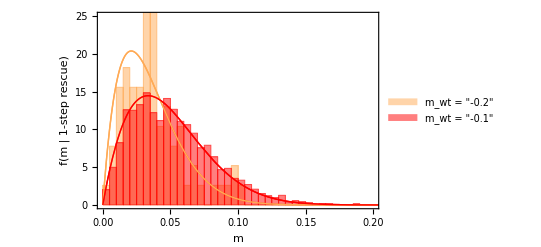

```mathematica
n=4;η=n/2;(*phenotypic dimensions*)
Es=0.01;(*mean mutational selective efffect*)
λ=2Es/n;(*mutational variance, i.e., scaled size*)
uo=0 UnitVector[n,1];(*mean mutational size; set to all zeros*)
n0=10^4;
U=10^-2;

mmax=0.5; (*max growth rate*)
mwts={(*-0.3,*)-0.2,-0.1};nmwts=Length[mwts];(*scaled*)
color={(*Darker[Blue,0.7],*)Lighter[Orange],Red};(*colors*)
zis=Table[√(2(mmax-mwts[[i]]))UnitVector[n,1],{i,nmwts}];(*vector from wildtype from the optimum along trait 1 axis*)

nsims=10^3;
(*nsims=10^4;*)(*for manuscript figure; takes a long time*)

Rescuems={};
k=1;
While[k<nmwts+1,

enmuts=(n0 U)/(1-Exp[mwts[[k]]]);

rescuems={};
j=0;
While[j<nsims,

nmuts=RandomVariate[PoissonDistribution[enmuts]];
dz2=RandomReal[MultinormalDistribution[uo,λ Idn],nmuts];
ms=mwts[[k]]+ss[dz2,zis[[k]]];
rvs=RandomReal[1,nmuts];
fixs=Table[rvs[[i]]<(1-Exp[-2ms[[i]]])1HeavisideTheta[ms[[i]]],{i,nmuts}];
Table[If[fixs[[i]],AppendTo[rescuems,ms[[i]]]],{i,Length[ms]}];

j++
];

AppendTo[Rescuems,rescuems];
k++
]

Table[PmrescueApprox/.α->λ (1+2ϵ)/(1+ϵ)/.β->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax-mwts[[i]],{i,nmwts}];
theory=Plot[%,{m,0,mmax},PlotStyle->color,PlotRange->All,Frame->{True,True,False,False}];

legends=Table[Style[StringForm["m_wt = ``",NumberForm[mwts[[k]],3]],14],{k,nmwts}]; 
simuls=Histogram[Rescuems,50,"PDF",ChartStyle->color,PlotRange->{{0,mmax},All},ChartLegends->Placed[legends,{0.8,0.8}],Axes->False];

Show[{theory,simuls,theory},LabelStyle->styl,FrameLabel->{"m","f(m | 1-step rescue)"},PlotRange->{{0,0.2},{0,25}}]
(*Export[imagedir<>"fm1steprescue.pdf",%];*)

Clear[n,λ,mmax,n0,U,k,j]
```

we can speed things up by skipping the wildtype dynamics and just simualting a bunch of mutants and asking if they would establish

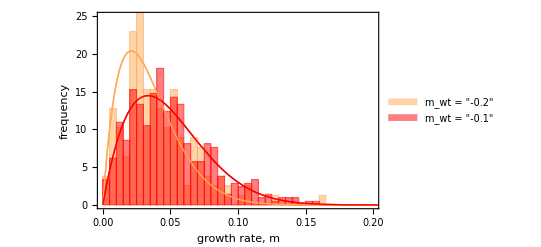

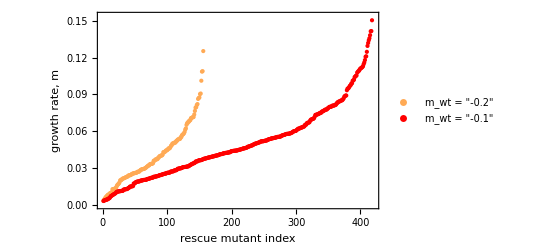

```mathematica
n=4;η=n/2;(*phenotypic dimensions*)
Es=0.01;(*mean mutational selective efffect*)
λ=2Es/n;(*mutational variance, i.e., scaled size*)
uo=0 UnitVector[n,1];(*mean mutational size; set to all zeros*)

mmax=0.5; (*max growth rate*)
mwts={(*-0.3,*)-0.2,-0.1};nmwts=Length[mwts];(*wildtype growth rates*)
color={(*Darker[Blue,0.7],*)Lighter[Orange],Red};(*colors*)
zis=Table[√(2(mmax-mwts[[i]]))UnitVector[n,1],{i,nmwts}];(*vector from wildtype from the optimum along trait 1 axis*)

nmuts={(*10^8,*)10^6,10^5};(*number of mutants to simulate for each mwt*)
(*nmuts={(*10^8,*)10^7,10^6};*)(*publication quality*)

Rescuems={};
k=1;
While[k<nmwts+1,

rescuems={};

dz2=RandomReal[MultinormalDistribution[uo,λ Idn],nmuts[[k]]];(*mutant phenotypes*)
ms=mwts[[k]]+ss[dz2,zis[[k]]];(*mutant growth rates*)
rvs=RandomReal[1,nmuts[[k]]];(*random #*)
fixs=Table[rvs[[i]]<(1-Exp[-2ms[[i]]])1HeavisideTheta[ms[[i]]],{i,nmuts[[k]]}];(*determine if establish*)
Table[If[fixs[[i]],AppendTo[rescuems,ms[[i]]]],{i,Length[ms]}];(*add growth rates of those that establish*)

AppendTo[Rescuems,rescuems];
k++
]

Table[PmrescueApprox/.α->λ (1+2ϵ)/(1+ϵ)/.β->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax-mwts[[i]],{i,nmwts}];
theory=Plot[%,{m,0,mmax},PlotStyle->color,PlotRange->All,Frame->{True,True,False,False}];

legends=Table[Style[StringForm["m_wt = ``",NumberForm[mwts[[k]],3]],14],{k,nmwts}]; 
simuls=Histogram[Rescuems,50,"PDF",ChartStyle->color,PlotRange->{{0,mmax},All},ChartLegends->Placed[legends,{0.8,0.8}],Axes->False];

Show[{theory,simuls,theory},LabelStyle->styl,FrameLabel->{Style["growth rate, m",14],Style["frequency",14]},PlotRange->{{0,0.2},{0,25}}]
(*Export[imagedir<>"fm1steprescue.pdf",%];*)

Table[Sort[Rescuems[[i]]],{i,Length[Rescuems]}];
ListPlot[%,PlotStyle->color,Frame->{True,True,False,False},FrameLabel->{Style["rescue mutant index",14],Style["growth rate, m",14]},LabelStyle->styl,PlotLegends->Placed[PointLegend[color,legends],Scaled@{0.8,0.15}]]
(*Export[imagedir<>"mascending.pdf",%];*)

Clear[n,λ,mmax,n0,U,k,j]
```

Let’s instead plot the distribution of s

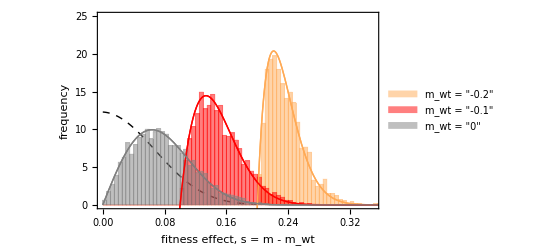

```mathematica
n=4;η=n/2;(*phenotypic dimensions*)
Es=0.01;(*mean mutational selective efffect*)
λ=2Es/n;(*mutational variance, i.e., scaled size*)
uo=0 UnitVector[n,1];(*mean mutational size; set to all zeros*)

mmax=0.5; (*max growth rate*)
mwts={(*-0.3,*)-0.2,-0.1,0};nmwts=Length[mwts];(*wildtype growth rates*)
color={(*Darker[Blue,0.7],*)Lighter[Orange],Red, Gray};(*colors*)
zis=Table[√(2(mmax-mwts[[i]]))UnitVector[n,1],{i,nmwts}];(*vector from wildtype from the optimum along trait 1 axis*)

nmuts={(*10^8,*)10^5,10^5,10^5};(*number of mutants to simulate for each mwt*)
(*nmuts={(*10^8,*)10^7,10^6,10^5};*)(*for publication quality*)

Rescuems={};
k=1;
While[k<nmwts+1,

rescuems={};

dz2=RandomReal[MultinormalDistribution[uo,λ Idn],nmuts[[k]]];(*mutant phenotypes*)
ms=mwts[[k]]+ss[dz2,zis[[k]]];(*mutant growth rates*)
rvs=RandomReal[1,nmuts[[k]]];(*random #*)
fixs=Table[rvs[[i]]<(1-Exp[-2ms[[i]]])1HeavisideTheta[ms[[i]]],{i,nmuts[[k]]}];(*determine if establish*)
Table[If[fixs[[i]],AppendTo[rescuems,ms[[i]]-mwts[[k]]]],{i,Length[ms]}];(*add growth rates of those that establish*)

AppendTo[Rescuems,rescuems];
k++
]

Table[PmrescueApprox/.α->λ (1+2ϵ)/(1+ϵ)/.β->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax-mwts[[i]]/.m->mwts[[i]]+s,{i,nmwts}];
theory=Plot[%,{s,0,mmax-Min[mwts]},PlotStyle->color,PlotRange->All,Frame->{True,True,False,False}];

legends=Table[Style[StringForm["m_wt = ``",NumberForm[mwts[[k]],3]],14],{k,nmwts}]; 
simuls=Histogram[Rescuems,50,"PDF",ChartStyle->color,PlotRange->{{0,mmax-Min[mwts]},All},ChartLegends->Placed[legends,{0.2,0.8}],Axes->False];

fm[m,mwt,mmax,λ,n]/.m->s-mwt/.mwt->0;
%/NIntegrate[%,{s,0,∞}];
fisher=Plot[%,{s,0,0.2},PlotStyle->{Black,Dashed,Thick}];

Show[{theory,fisher,simuls,theory},LabelStyle->styl,FrameLabel->{Style["fitness effect, s = m - m_wt",14],Style["frequency",14]},PlotRange->{{0,0.35},{0,25}}]
(*Export[imagedir<>"fs1steprescue.pdf",%];*)

Clear[n,λ,mmax,n0,U,k,j,Es]
```

This is analgous to the Fisher to Kimura adjustment, where we’ve multiplied Martin & Lenormand (2015)’s pdf of m by 1-Exp[-2m] (or 0 if m<0; and normalized back into a pdf) to weight by the probability of fixation.

### Probability a mutation of scaled size x rescues the population

According to Fisher 1930 (see Orr 1998 for review), the probability a mutation of scaled size x=r√n/d, where n is the number of dimensions and d is twice the distance to the optimum, is beneficial is

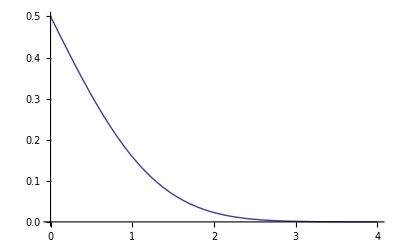

```mathematica
(1-CDF[NormalDistribution[0,1],x]);
Plot[%,{x,0,4}]
```

giving pdf

√(2 π) (1-1/2 Erfc[-x/(√2)])

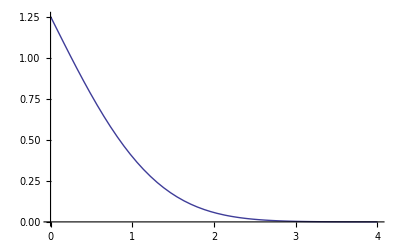

```mathematica
(1-CDF[NormalDistribution[0,1],x]);
Integrate[%,{x,0,∞}];
%%/%
Plot[%,{x,0,4}]
```

Following Kimura 1983 (again, see Orr 1998 for review), if the probability of fixation for a given x that is beneficial is roughly proportional to 2x, then the pdf of mutants that fix is

4 x (1-1/2 Erfc[-x/(√2)])

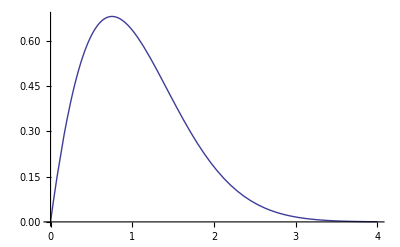

```mathematica
2x(1-CDF[NormalDistribution[0,1],x]);
Integrate[%,{x,0,∞}];
%%/%
Plot[%,{x,0,4}]
```

In our case we additionally need x to be large enough that it gives a positive growth rate. Given the radius of the zero-growth sphere (phenotypic distance from optimum to zero growth) is ro, the probability of rescue given beneficial r is roughly 2(ro - d/2 + r) when it is small but positive (that is, d/2-r, the remaining distance to the optimum, is less than ro, the distance from the optimum to zero growth). Let d/2-ro=rd, the distance from the wildtype to zero growth. Then scaling this by mutliplying by √n/d, we have 2((ro √n)/d-(d/2 √n)/d+x) = 2(x-rd(√n)/d)=2(x-xd), reducing to Kimura 1983 when the wildtype has a growth rate of zero xd=0, and the pdf of x given rescue is

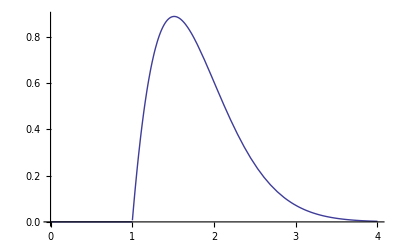

```mathematica
2(x-xd)(1-CDF[NormalDistribution[0,1],x])HeavisideTheta[x-xd]/.xd->1;
NIntegrate[%,{x,0,∞}];
%%/%;
Plot[%,{x,0,4},PlotRange->{0,All}]
```

This pushes the left hand side of Kimura’s distribution to the right, building up mass at higher values, but does not affect the right hand side much -- ie rescue increases the mean size of mutations observed (not the max) and also decreases the variance.

Note that this could be improved by including the angle of the mutation, as the mutant will not fall exactly on the line connecting the wildtype to the optimum.

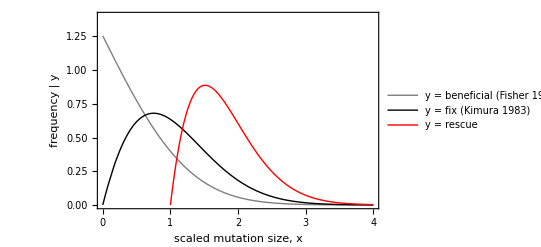

```mathematica
(1-CDF[NormalDistribution[0,1],x]);
Integrate[%,{x,0,∞}];
%%/%;
fisher=Plot[%,{x,0,4},PlotStyle->{Thick,Gray}];

2x(1-CDF[NormalDistribution[0,1],x]);
Integrate[%,{x,0,∞}];
%%/%;
kimura=Plot[%,{x,0,4},PlotStyle->{Thick,Black}];

2(x-xd)(1-CDF[NormalDistribution[0,1],x])HeavisideTheta[x-xd]/.xd->1;
NIntegrate[%,{x,0,∞}];
%%/%;
us=Plot[%,{x,1,4},PlotRange->{0,All},PlotStyle->{Thick,Red}];

Legended[Show[fisher,kimura,us,Frame->{True,True,False,False},FrameLabel->{Style["scaled mutation size, x",16],Style["frequency | y",16]}, PlotRange->{0,1.4},LabelStyle->16],Placed[LineLegend[{Directive[Thick,Gray],Directive[Thick,Black],Directive[Thick,Red]},{Style["y = beneficial (Fisher 1930)",16],Style["y = fix (Kimura 1983)",16],Style["y = rescue",16]}],Scaled@{0.65,0.8}]]
(*Export[imagedir<>"EffectSize3.pdf",%];*)
```

## (b) 2-step rescue

(b) What is the probability that at least one single mutant lineage is not directly successful but produces a double mutant lineage which is?

### Set-up

This is roughly the integral over m1 (the growth rate of the single mutant) of: (A) the expected number of mutations from the wildtype that give a growth rate m1, times (B) the probability a mutant with growth rate m1 is not directly successful, times (C) the expected number of individuals arising in a lineage with growth rate m1 that is not directly successful, times (D) the probability an individual with growth rate m1 produces a mutant lineage that is directly successful.

If f[m|m_wt] is the pdf of mutant growth rates given wildtype growth rate, then (A) is just (n0 U)/m_wt f[m1 | m_wt] dm1.

Meanwhile, (B) is just 1 minus the probability a lineage is successful, 1-P_est(m1); this is 1 when m1<0 and roughly Exp[-2m1] when m1>0.

From the previous section we know that (D) is U (∫_o)^∞ P_est(m2) f[m2 | m1] dm2, but we need to condition on m1 instead of mwt (this can introduce some complications, see below).

What remains to be calculated is (C), the expected number of individuals arising in a lineage with growth rate m1 that is not directly successful. This depends on whether a mutant is near critical m1~0 or sufficiently subcritical m1<<0  (sufficiently supercritical mutations will nearly always establish and rescue the population in 1-step).

### Sufficiently subcritical vs. sufficiently critical

The probability a lineage persists till time 2T << |1/m| (ie while it still behaves “critically”) is roughly

```mathematica
pestapp1/.t->2T
```

1/T

Given it does so the expected population size at time 2T is

```mathematica
Sum[n pntgtapp1,{n,0,∞}]/.t->2T//Simplify
```

1+T

and so the population size increases roughly linearly with time.

For T >>1 this is roughly

```mathematica
Sum[n pntgtapp1,{n,0,∞}]/.t->2T;
Normal[Series[%/.T->T/ϵ,{ϵ,0,-1}]]/.ϵ->1
```

T

Thus if a lineage persists for time T (with probability roughly 1/T while T<< |1/m| ) it will have a cumulative number of individuals

```mathematica
Sum[n pntgtapp1,{n,0,∞}];
Normal[Series[%/.t->t/ϵ,{ϵ,0,-1}]]/.ϵ->1;
Sum[%,{t,0,2T}];
%/. 1+2T->2T
```

T^2

Below we see that while the probability of persisting for time 2T (blue) declines like 1/T, the “weight” of such a lineage (red; cumulative number of individuals) increases like T^2, and thus the majority of the “weight” is contributed by rare long lived lineages (black).

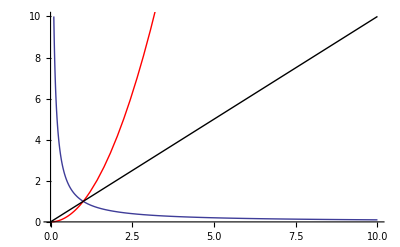

```mathematica
Show[
Plot[1/T,{T,0,10},PlotRange->{0,10}],
Plot[T^2,{T,0,10},PlotStyle->Red],
Plot[T,{T,0,10},PlotStyle->{Black,Thick}],
PlotRange->{0,10}
]
```

The probability that a lineage with cumulative number of individuals T^2 leads to rescue is

```mathematica
1-Expectation[z^x,x\[Distributed]PoissonDistribution[U T^2 p]]/.z->0
```

1-ⅇ^(-p T^2 U)

where p is the probability a mutant produced from this lineage rescues the population.

When T^2 U p <1 this is roughly

```mathematica
Normal[Series[1-Exp[-T^2 U p]/.U->U ϵ,{ϵ,0,1}]]/.ϵ->1
```

p T^2 U

This increases quickly from 0 to 1 with T (as T is squared). For this to be near one we need

```mathematica
Simplify[Solve[T^2 U p==1,T][[2]],{p>0,U>0,T>0}]
```

{T→1/(√(p U))}

and this occurs with probability

```mathematica
pestapp1/.t->1/√(p U)
```

2 √(p U)

### 2-step critical

#### Probability of rescue

Given that only those near critical lineages which persist “critically” for a long enough time to make rescue almost guaranteed (that is,for time  1/√(p U)) produce rescue mutants, the probability a single mutant with growth rate -√(p U)<m_1<√(p U) produces a double mutant that rescues the population is 2 √(p U).

It is now very important to recall that p depends on m_1, so let’s write p=p_m_1. When -√(p_m_1 U)<m_1<√(p_m_1 U) holds (equivalently, m_1^2<p_m_1 U) , the rate of 2-step critical rescue through m1 (given it arises) is  f(m_1|m_wt)  2 √(p_m_1 U) when m_1 < 0 and  f(m_1|m_wt) Exp[-2 m_1] 2 √(p_m_1 U) when m_1>0. We’d then like to integrate these over m_1, but the trouble is that our integration limits depend on m_1. We will here make the assumption that sufficiently critical m_1 are very small (e.g., U or Es is small enough so that single mutants need to drift for a relatively long time to produce a successful double mutant), so that our zeroth order approximation for the integration limits can be used.

As derived in the 1-step case (here using m1 instead of mwt), using the negative gamma we have an approximation for p

```mathematica
Clear[mmax,Es]
(1-Exp[-2m2]) Simplify[PDF[TransformedDistribution[so-γ,γ\[Distributed]GammaDistribution[β,α]],s],so-s>0]/.so->mmax-m1/.s->m2-m1/.α->Subscript[α, m1]/.β->Subscript[β, m1];
p2succ=Simplify[Integrate[%,{m2,0,mmax}],{mmax>0,Subscript[α, m1]>0,Subscript[β, m1]>0}]
(*%/.α->λ (1+2ϵ)/(1+ϵ)/.β->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax*)
```

1+(-Gamma[β_m1,mmax/α_m1]+ⅇ^(-2 mmax) Gamma[β_m1,mmax (-2+1/α_m1)] (1-2 α_m1)^-β_m1)/Gamma[β_m1]-ⅇ^(-2 mmax) (1-2 α_m1)^-β_m1

where α_m1 and β_m1 depend on so = mmax - m1.

There are a number of options to solve √(U p_m_1)=m_1 for m_1. The simplest is to take a series of p_m_1 in m_1 around 0 to the zeroth order. This drops all m1 dependence

```mathematica
m1crit0=√(U p2succ)/.Subscript[α, m1]->Subscript[α, 0]/.Subscript[β, m1]->Subscript[β, 0]
```

√(U (1+(-Gamma[β_0,mmax/α_0]+ⅇ^(-2 mmax) Gamma[β_0,mmax (-2+1/α_0)] (1-2 α_0)^-β_0)/Gamma[β_0]-ⅇ^(-2 mmax) (1-2 α_0)^-β_0))

If m1 can be larger, eg if the mutation rate is large then single mutants don’t need to drift as long, then we might take the first order approximation (whose expression is ugly)

```mathematica
Normal[Series[U p2succ/.Subscript[α, 0]->Subscript[α, m1]/.Subscript[β, 0]->Subscript[β, m1]/.Subscript[α, m1]->λ (1+2ϵ)/(1+ϵ)/.Subscript[β, m1]->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax-m1,{m1,0,1}]];
m1crit1=Solve[m1^2==%,m1];
```

Lets see now see how good these are at estimating the true threshold m1. 

When U<Uc the zeroth order is great (compare blue to green):

```mathematica
p2succ^(1/2)/.Subscript[α, 0]->Subscript[α, m1]/.Subscript[β, 0]->Subscript[β, m1]/.Subscript[α, m1]->λ (1+2ϵ)/(1+ϵ)/.Subscript[β, m1]->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax-m1/.λ->2Es/n//Simplify
```

√(1-ⅇ^(-2 mmax) (1-(4 Es (Es-2 m1+2 mmax))/((Es-m1+mmax) n))^(-((Es-m1+mmax)^2 n)/(2 Es (Es-2 m1+2 mmax)))+(-Gamma[((Es-m1+mmax)^2 n)/(2 Es (Es-2 m1+2 mmax)),(mmax (Es-m1+mmax) n)/(2 Es (Es-2 m1+2 mmax))]+ⅇ^(-2 mmax) (1-(4 Es (Es-2 m1+2 mmax))/((Es-m1+mmax) n))^(-((Es-m1+mmax)^2 n)/(2 Es (Es-2 m1+2 mmax))) Gamma[((Es-m1+mmax)^2 n)/(2 Es (Es-2 m1+2 mmax)),mmax (-2+((Es-m1+mmax) n)/(2 Es (Es-2 m1+2 mmax)))])/Gamma[((Es-m1+mmax)^2 n)/(2 Es (Es-2 m1+2 mmax))])

-0.00286901

0.003027

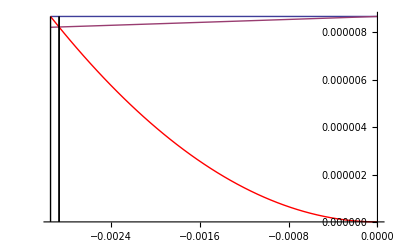

```mathematica
params={Es->0.01, n->4, mmax->0.5,n0->10^4,U->10^-2 Uc,mwt->-0.1};

true=m1/.FindRoot[U p2succ-m1^2/.Subscript[α, 0]->Subscript[α, m1]/.Subscript[β, 0]->Subscript[β, m1]/.Subscript[α, m1]->λ (1+2ϵ)/(1+ϵ)/.Subscript[β, m1]->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax-m1/.λ->2Es/n/.params/.Uc->n^2 λ/4/.λ->2Es/n/.params,{m1,-0.02}]
m1/.FindRoot[U p2succ-m1^2/.Subscript[α, 0]->Subscript[α, m1]/.Subscript[β, 0]->Subscript[β, m1]/.Subscript[α, m1]->λ (1+2ϵ)/(1+ϵ)/.Subscript[β, m1]->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax-m1/.λ->2Es/n/.params/.Uc->n^2 λ/4/.λ->2Es/n/.params,{m1,0.02}]
approx0=-m1crit0/.Subscript[α, 0]->λ (1+2ϵ)/(1+ϵ)/.Subscript[β, 0]->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax/.λ->2Es/n/.params/.Uc->n^2 λ/4/.λ->2Es/n/.params;

approx1=Select[m1/.m1crit1/.λ->2Es/n/.params/.Uc->n^2 λ/4/.λ->2Es/n/.params,#<0&][[1]];


U p2succ/.Subscript[α, 0]->Subscript[α, m1]/.Subscript[β, 0]->Subscript[β, m1]/.Subscript[α, m1]->λ (1+2ϵ)/(1+ϵ)/.Subscript[β, m1]->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax-m1/.λ->2Es/n/.params/.Uc->n^2 λ/4/.λ->2Es/n/.params/.m1->{0,m1};
Show[
Plot[%,{m1,approx0,0}],
Plot[m1^2,{m1,approx0,0},PlotStyle->Red],
Epilog->{
Style[Line[{{true,0},{true,approx0^2}}], Purple],
Style[Line[{{approx0,0},{approx0,approx0^2}}],Blue],
Style[Line[{{approx1,0},{approx1,approx0^2}}],Green]
},
PlotRange->{0,All},
AxesOrigin->{0,0}
]
```

When U~Uc the zeroth order still does fine (although the first order, purple, is much better)

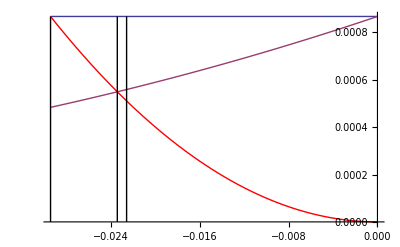

```mathematica
params={Es->0.01, n->4, mmax->0.5,n0->10^4,U->10^0 Uc,mwt->-0.1};

true=m1/.FindRoot[U p2succ-m1^2/.Subscript[α, 0]->Subscript[α, m1]/.Subscript[β, 0]->Subscript[β, m1]/.Subscript[α, m1]->λ (1+2ϵ)/(1+ϵ)/.Subscript[β, m1]->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax-m1/.λ->2Es/n/.params/.Uc->n^2 λ/4/.λ->2Es/n/.params,{m1,-0.02}];

approx0=-m1crit0/.Subscript[α, 0]->λ (1+2ϵ)/(1+ϵ)/.Subscript[β, 0]->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax/.λ->2Es/n/.params/.Uc->n^2 λ/4/.λ->2Es/n/.params;

approx1=Select[m1/.m1crit1/.λ->2Es/n/.params/.Uc->n^2 λ/4/.λ->2Es/n/.params,#<0&][[1]];


U p2succ/.Subscript[α, 0]->Subscript[α, m1]/.Subscript[β, 0]->Subscript[β, m1]/.Subscript[α, m1]->λ (1+2ϵ)/(1+ϵ)/.Subscript[β, m1]->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax-m1/.λ->2Es/n/.params/.Uc->n^2 λ/4/.λ->2Es/n/.params/.m1->{0,m1};
Show[
Plot[%,{m1,approx0,0}],
Plot[m1^2,{m1,approx0,0},PlotStyle->Red],
Epilog->{
Style[Line[{{true,0},{true,approx0^2}}], Purple],
Style[Line[{{approx0,0},{approx0,approx0^2}}],Blue],
Style[Line[{{approx1,0},{approx1,approx0^2}}],Green]
},
PlotRange->{0,All},
AxesOrigin->{0,0}
]
```

When U>Uc the zeroth order is not much good and we will have to go with a higher order approximation (such as the first order approx) or the true numerical value

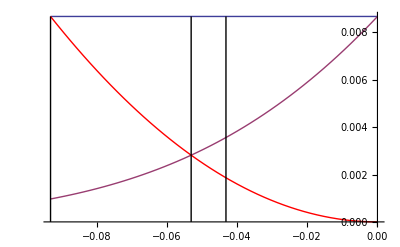

```mathematica
params={Es->0.01, n->4, mmax->0.5,n0->10^4,U->10^1 Uc,mwt->-0.1};

true=m1/.FindRoot[U p2succ-m1^2/.Subscript[α, 0]->Subscript[α, m1]/.Subscript[β, 0]->Subscript[β, m1]/.Subscript[α, m1]->λ (1+2ϵ)/(1+ϵ)/.Subscript[β, m1]->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax-m1/.λ->2Es/n/.params/.Uc->n^2 λ/4/.λ->2Es/n/.params,{m1,-0.02}];

approx0=-m1crit0/.Subscript[α, 0]->λ (1+2ϵ)/(1+ϵ)/.Subscript[β, 0]->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax/.λ->2Es/n/.params/.Uc->n^2 λ/4/.λ->2Es/n/.params;

approx1=Select[m1/.m1crit1/.λ->2Es/n/.params/.Uc->n^2 λ/4/.λ->2Es/n/.params,#<0&][[1]];


U p2succ/.Subscript[α, 0]->Subscript[α, m1]/.Subscript[β, 0]->Subscript[β, m1]/.Subscript[α, m1]->λ (1+2ϵ)/(1+ϵ)/.Subscript[β, m1]->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax-m1/.λ->2Es/n/.params/.Uc->n^2 λ/4/.λ->2Es/n/.params/.m1->{0,m1};
Show[
Plot[%,{m1,approx0,0}],
Plot[m1^2,{m1,approx0,0},PlotStyle->Red],
Epilog->{
Style[Line[{{true,0},{true,approx0^2}}], Purple],
Style[Line[{{approx0,0},{approx0,approx0^2}}],Blue],
Style[Line[{{approx1,0},{approx1,approx0^2}}],Green]
},
PlotRange->{0,All},
AxesOrigin->{0,0}
]
```

Starting with the slightly subcritical, what we want to integrate from -∞ to -m1^* is

```mathematica
Simplify[PDF[TransformedDistribution[so-γ,γ\[Distributed]GammaDistribution[β,α]],s],so-s>0]/.so->mmax-mwt/.s->m1-mwt/.α->Subscript[α, mwt]/.β->Subscript[β, mwt];
% 2 √(U p2succ)
(*Integrate[%,{m1,-∞,-a},Assumptions->a>0]*)
```

(2 ⅇ^((m1-mmax)/α_mwt) (-m1+mmax)^(-1+β_mwt) √(U (1+(-Gamma[β_m1,mmax/α_m1]+ⅇ^(-2 mmax) Gamma[β_m1,mmax (-2+1/α_m1)] (1-2 α_m1)^-β_m1)/Gamma[β_m1]-ⅇ^(-2 mmax) (1-2 α_m1)^-β_m1)) α_mwt^-β_mwt)/Gamma[β_mwt]

This can’t be done. We can try dopping the m_1 dependence in the α and β terms as we’ve done with the integration limits. This can be integrated

```mathematica
Simplify[PDF[TransformedDistribution[so-γ,γ\[Distributed]GammaDistribution[β,α]],s],so-s>0]/.so->mmax-mwt/.s->m1-mwt/.α->Subscript[α, mwt]/.β->Subscript[β, mwt];
 % 2 √(U p2succ)/.Subscript[α, m1]->Subscript[α, 0]/.Subscript[β, m1]->Subscript[β, 0];
slightlysubcriticalrate=Integrate[%,{m1,-a,0},Assumptions->{a>0,Subscript[α, mwt]>0,mmax>0}]
```

(2 (Gamma[β_mwt,mmax/α_mwt]-Gamma[β_mwt,(a+mmax)/α_mwt]) √(U (1+(-Gamma[β_0,mmax/α_0]+ⅇ^(-2 mmax) Gamma[β_0,mmax (-2+1/α_0)] (1-2 α_0)^-β_0)/Gamma[β_0]-ⅇ^(-2 mmax) (1-2 α_0)^-β_0)))/Gamma[β_mwt]

Let’s try the same approximation for the slightly supercritical (where we need an extra term to make sure these don’t rescue the population in 1-step)

```mathematica
Simplify[PDF[TransformedDistribution[so-γ,γ\[Distributed]GammaDistribution[β,α]],s],so-s>0]/.so->mmax-mwt/.s->m1-mwt/.α->Subscript[α, mwt]/.β->Subscript[β, mwt];
 % Exp[-2m1]2 √(U p2succ)/.Subscript[α, m1]->Subscript[α, 0]/.Subscript[β, m1]->Subscript[β, 0];
slightlysupercriticalrate=Integrate[%,{m1,0,a},Assumptions->{a>0,Subscript[α, mwt]>0,mmax>0,a<mmax}]
```

-1/Gamma[β_mwt]2 ⅇ^(-2 mmax) (Gamma[β_mwt,mmax (-2+1/α_mwt)]-Gamma[β_mwt,((a-mmax) (-1+2 α_mwt))/α_mwt]) √(U (1+(-Gamma[β_0,mmax/α_0]+ⅇ^(-2 mmax) Gamma[β_0,mmax (-2+1/α_0)] (1-2 α_0)^-β_0)/Gamma[β_0]-ⅇ^(-2 mmax) (1-2 α_0)^-β_0)) (1-2 α_mwt)^-β_mwt

Putting this all together, the rate at which near critical mutants do not directly rescue but lead to 2-step rescue is roughly

```mathematica
criticalrate=slightlysubcriticalrate+slightlysupercriticalrate//Simplify
```

1/Gamma[β_mwt]2 ⅇ^(-2 mmax) √(U (1+(-Gamma[β_0,mmax/α_0]+ⅇ^(-2 mmax) Gamma[β_0,mmax (-2+1/α_0)] (1-2 α_0)^-β_0)/Gamma[β_0]-ⅇ^(-2 mmax) (1-2 α_0)^-β_0)) (-Gamma[β_mwt,mmax (-2+1/α_mwt)]+Gamma[β_mwt,((a-mmax) (-1+2 α_mwt))/α_mwt]+ⅇ^(2 mmax) (Gamma[β_mwt,mmax/α_mwt]-Gamma[β_mwt,(a+mmax)/α_mwt]) (1-2 α_mwt)^β_mwt) (1-2 α_mwt)^-β_mwt

where a is the zeroth order approximation for the threshold m1.

Lets see how the zeroth order approximation of the integration limits does

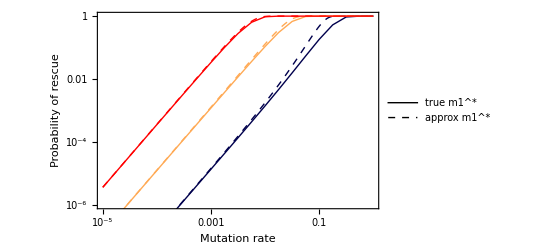

```mathematica
mwts={-0.3,-0.2,-0.1};nmwts=Length[mwts];(*wildtype growth rates*)
color={Darker[Blue,0.7],Lighter[Orange],Red};(*colors*)
colordashed={{Darker[Blue,0.7],Dashed},{Lighter[Orange],Dashed},{Red,Dashed}};(*colors*)
colorthick={{Darker[Blue,0.7],Thick},{Lighter[Orange],Thick},{Red,Thick}};(*colors*)
params={Es->0.01,mmax->0.5,n->4,n0->10^4};

((n0 U)/(1-Exp[mwt]))criticalrate/.a->m1crit0/.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params;
Table[1-Exp[- %]/.mwt->mwts[[i]],{i,nmwts}];

twostepcritical=
LogLogPlot[%,{U,10^-5,10^0},PlotStyle->colordashed,Frame->{True,True,False,False},PlotRange->{10^-6,1}];

critm1eqn=U p2succ-m1^2/.U->10^c /.Subscript[α, m1]->λ (1+2ϵ)/(1+ϵ)/.Subscript[β, m1]->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax-m1/.λ->2Es/n/.params;
rate2better=((n0 U)/(1-Exp[mwt]))criticalrate/.U->10^c /.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params;

Table[{
10^c,

truem1crit=m1/.FindRoot[critm1eqn,{m1,-0.02}];

1-Exp[-rate2better/.mwt->mwts[[i]]/.a->-truem1crit]
},
{i,nmwts},
{c,-5,0,0.25}
];
twostepcriticalbetter=ListLogLogPlot[%,Joined->True,PlotStyle->color];

Legended[
Show[
twostepcritical,
twostepcriticalbetter,
FrameStyle->Directive[14],
FrameLabel->{Style["Mutation rate",14],Style["Probability of rescue",14]},
PlotRangePadding->None
],
Placed[
LineLegend[{Directive[Black],Directive[Dashed]},{"true m1^*","approx m1^*"},LegendLayout->"Row"],
Top]
]
```

So the integration bound is a fine approximation.

We can also try numerically integrating over m1 instead of dropping the m1 dependence in α_m1 and β_m1

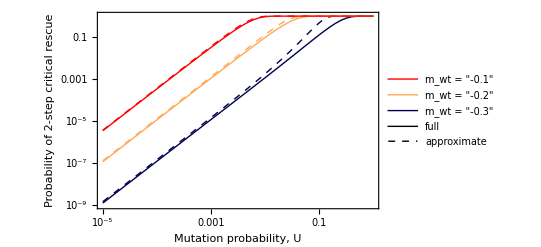

```mathematica
mwts={-0.3,-0.2,-0.1};nmwts=Length[mwts];(*wildtype growth rates*)
color={Darker[Blue,0.7],Lighter[Orange],Red};(*colors*)
colordashedthick={{Darker[Blue,0.7],Dashed,Thick},{Lighter[Orange],Dashed,Thick},{Red,Dashed,Thick}};(*colors*)
params={Es->0.01,mmax->0.5,n->4,n0->10^4};
colorthick={Directive[Thick,Darker[Blue,0.7]],Directive[Thick,Lighter[Orange]],Directive[Thick,Red]};(*colors*)
styl={FontFamily-> "Times",FontSize->14};(*styles of axes and legend*)
legends=Table[Style[StringForm["m_wt = ``",NumberForm[mwts[[i]],3]],14],{i,nmwts}]; 
(*nint=0.1;*)(*publication quality*)
nint=1;

critm1eqn=U p2succ-m1^2/.U->10^c/.Subscript[α, m1]->λ (1+2ϵ)/(1+ϵ)/.Subscript[β, m1]->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax-m1/.λ->2Es/n/.params;

Simplify[PDF[TransformedDistribution[so-γ,γ\[Distributed]GammaDistribution[β,α]],s],so-s>0]/.so->mmax-mwt/.s->m1-mwt/.α->Subscript[α, mwt]/.β->Subscript[β, mwt];
rsub=U% 2 √(U p2succ)(*/.a->-m1crit0*)(*/.Subscript[α, m1]->Subscript[α, 0]*)(*/.Subscript[β, m1]->Subscript[β, 0]*)/.U->10^c/.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params;
Simplify[PDF[TransformedDistribution[so-γ,γ\[Distributed]GammaDistribution[β,α]],s],so-s>0]/.so->mmax-mwt/.s->m1-mwt/.α->Subscript[α, mwt]/.β->Subscript[β, mwt];
rsup=U%Exp[-2m1] 2 √(U p2succ)(*/.Subscript[α, m1]->Subscript[α, 0]*)(*/.Subscript[β, m1]->Subscript[β, 0]*)/.U->10^c/.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params;

Table[
{
10^c,
truem1crit=m1/.FindRoot[critm1eqn,{m1,-0.02}](*-m1crit0/.U->10^c Uc/.Uc->n^2 λ/4/.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params*);
nrate12=NIntegrate[ rsub/.mwt->mwts[[i]],{m1,truem1crit,0}](*slightlysubcriticalrate*)+NIntegrate[rsup/.mwt->mwts[[i]],{m1,0,-truem1crit}](*slightlysupercriticalrate*)(*/.a->-m1crit0/.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params*);(*criticalrate/.a->-m1crit0/.U->10^c Uc/.Uc->n^2 λ/4/.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params*)
1-Exp[-(-n0/mwt)nrate12]/.U->10^c/.λ->2Es/n/.params/.mwt->mwts[[i]]
},
{i,nmwts},
{c,-5,0,nint}
];

real=ListLogLogPlot[%,PlotStyle->colorthick,Joined->True];

((n0 U)/(1-Exp[mwt]))criticalrate(*slightlysubcriticalrate*)/.a->m1crit0/.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params;
Table[1-Exp[- %]/.mwt->mwts[[i]],{i,nmwts}];

twostepcritical=
LogLogPlot[%,{U,10^-5,10^0},PlotStyle->colordashedthick,Frame->{True,True,False,False},PlotRange->{10^-9,1},FrameLabel->{"",""}];

Legended[
Show[
twostepcritical,
real,
FrameStyle->Directive[14],
FrameLabel->{Style["Mutation probability, U",14],Style["Probability of 2-step
 critical rescue",14]},
PlotRangePadding->None
],
{
Placed[
LineLegend[{Directive[Black,Thick],Directive[Dashed,Thick]},{Style["full",14],Style["approximate",14]},LegendLayout->"Row"],
Top
],
Placed[
LineLegend[Reverse[colorthick],Reverse[legends]],
Scaled@{0.8,0.3}
]
}
]
(*Export[imagedir<>"2stepCriticalApprox.pdf",%];*)
```

Once again this is a fine approximation. To summarize, a decent approximation for the rate of 2-step critical rescue given a first step mutation arises  (including both slightly super- and slightly sub-critical single mutants), given the reasoning of Weissman et al 2009 TPB holds, is

```mathematica
criticalrate/.a->m1crit0//Simplify
```

1/Gamma[β_mwt]2 ⅇ^(-2 mmax) √(U (1+(-Gamma[β_0,mmax/α_0]+ⅇ^(-2 mmax) Gamma[β_0,mmax (-2+1/α_0)] (1-2 α_0)^-β_0)/Gamma[β_0]-ⅇ^(-2 mmax) (1-2 α_0)^-β_0)) (-Gamma[β_mwt,mmax (-2+1/α_mwt)]+Gamma[β_mwt,((-mmax+√(U (1+(-Gamma[β_0,mmax/α_0]+ⅇ^(-2 mmax) Gamma[β_0,mmax (-2+1/α_0)] (1-2 α_0)^-β_0)/Gamma[β_0]-ⅇ^(-2 mmax) (1-2 α_0)^-β_0))) (-1+2 α_mwt))/α_mwt]+ⅇ^(2 mmax) (Gamma[β_mwt,mmax/α_mwt]-Gamma[β_mwt,(mmax+√(U (1+(-Gamma[β_0,mmax/α_0]+ⅇ^(-2 mmax) Gamma[β_0,mmax (-2+1/α_0)] (1-2 α_0)^-β_0)/Gamma[β_0]-ⅇ^(-2 mmax) (1-2 α_0)^-β_0)))/α_mwt]) (1-2 α_mwt)^β_mwt) (1-2 α_mwt)^-β_mwt

#### Distribution of fitness effects of rescue genotypes following rescue

Given that 2-step rescue occurs through a near critical single mutant (m1~0), the distribution of double mutant growth rates (that is, individual growth rates) is roughly f(m_2 | critical 2-step rescue) = (f(m_2| 0)P(rescue | m_2))/(P(critical 2-step rescue)), which does not depend on the wildtype (stress).

From the Feller diffusion the probability of rescue given a double mutant with growth rate m arises is just

```mathematica
Prescuem2=1-Exp[-2m]
```

1-ⅇ^(-2 m)

The probability of rescue is this times f(m|0) integrated over all m>0. We once again use the approximation from Martin & Lenormand 2006 (which in this case is very good as the single mutant is near critical)

```mathematica
Simplify[PDF[TransformedDistribution[so-γ,γ\[Distributed]GammaDistribution[β,α]],s],so-s>0]/.so->mmax-mwt/.s->m-mwt/.mwt->0;
PrescueApprox=Integrate[Prescuem2%,{m,0,mmax},Assumptions->{mmax>0,β>0,α>0}]
```

1+(ⅇ^(-2 mmax) (1-2 α)^-β (-Gamma[β]+Gamma[β,mmax (-2+1/α)]))/Gamma[β]-Gamma[β,mmax/α]/Gamma[β]

We then have an approximation for the distribution of m given rescue

```mathematica
Simplify[PDF[TransformedDistribution[so-γ,γ\[Distributed]GammaDistribution[β,α]],s],so-s>0]/.so->mmax-mwt/.s->m-mwt/.mwt->0;
PmrescueApprox=Simplify[(% Prescuem2)/PrescueApprox,{α>0,β>0,mmax>0}]
```

(ⅇ^((m-mmax)/α) (1-ⅇ^(-2 m)) (-m+mmax)^(-1+β) α^-β)/(Gamma[β] (1+(ⅇ^(-2 mmax) (1-2 α)^-β (-Gamma[β]+Gamma[β,mmax (-2+1/α)]))/Gamma[β]-Gamma[β,mmax/α]/Gamma[β]))

Compare to simulated mutant growth rates from a perfectly critical ancestor

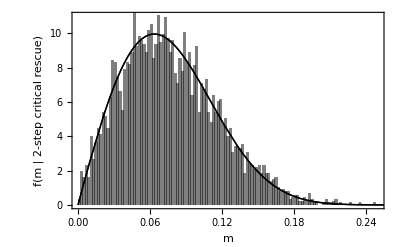

```mathematica
n=4;η=n/2;(*phenotypic dimensions*)
Es=0.01;(*mean mutational selective efffect*)
λ=2Es/n;(*mutational variance, i.e., scaled size*)
uo=0 UnitVector[n,1];(*mean mutational size; set to all zeros*)

mmax=0.5; (*max growth rate*)
mwts={-0.3(*,-0.2,-0.1,0*)};nmwts=Length[mwts];(*wildtype growth rates*)
color={Darker[Blue,0.7](*,Lighter[Orange],Red, Gray*)};(*colors*)
zis=√(2(mmax-0))UnitVector[n,1];(*vector from wildtype from the optimum along trait 1 axis*)
styl={FontFamily-> "Times",FontSize->14};(*styles of axes and legend*)
legends=Table[Style[StringForm["m_wt = ``",NumberForm[mwts[[i]],3]],14],{i,nmwts}]; 

nmuts=10^5;(*number of mutants to simulate for each mwt*)

Rescuems={};
k=1;
While[k<nmwts+1,

rescuems={};

dz2=RandomReal[MultinormalDistribution[uo,λ Idn],nmuts];(*mutant phenotypes*)
ms=ss[dz2,zis];(*mutant fitness effects*)
rvs=RandomReal[1,nmuts];(*random #*)
fixs=Table[rvs[[i]]<(1-Exp[-2ms[[i]]])1HeavisideTheta[ms[[i]]],{i,nmuts}];(*determine if establish*)
Table[If[fixs[[i]],AppendTo[rescuems,ms[[i]]]],{i,Length[ms]}];(*add fitness effect of those that establish*)

AppendTo[Rescuems,rescuems];
k++
]
PmrescueApprox/.α->λ (1+2ϵ)/(1+ϵ)/.β->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax-0;
theory=Plot[%,{m2,0,mmax},PlotStyle->Black,PlotRange->All,Frame->{True,True,False,False}];

(*legends=Table[Style[StringForm["m_wt = ``",NumberForm[mwts[[k]],3]],14],{k,nmwts}];*) 
(*Table[rescuems-mwts[[i]],{i,nmwts}];*)
simuls=Histogram[Rescuems,100,"PDF",ChartStyle->Black,PlotRange->{{0,mmax},All},(*ChartLegends->Placed[legends,{0.85,0.75}],*)Axes->False];

(*fm[m,mwt,mmax,λ,n]/.m->s-mwt/.mwt->0;
%/NIntegrate[%,{s,0,∞}];
fisher=Plot[%,{s,0,0.2},PlotStyle->{Black,Dashed,Thick}];
*)
Show[{theory,(*fisher,*)simuls,theory},LabelStyle->styl,FrameLabel->{Style["m",14],Style["f(m | 2-step critical rescue)",14]},PlotRange->{{0,0.25},{0,11}}]
Export[imagedir<>"fm2stepCritrescue.pdf",%];

Clear[n,λ,mmax,n0,U,k,j,Es]
```

in terms of s this is more interesting:

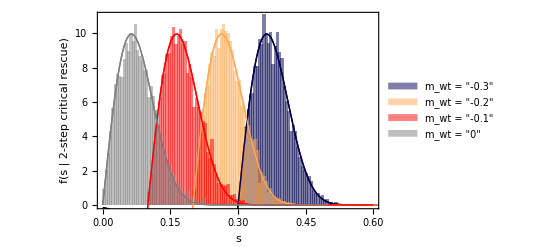

```mathematica
n=4;η=n/2;(*phenotypic dimensions*)
Es=0.01;(*mean mutational selective efffect*)
λ=2Es/n;(*mutational variance, i.e., scaled size*)
uo=0 UnitVector[n,1];(*mean mutational size; set to all zeros*)

mmax=0.5; (*max growth rate*)
mwts={-0.3,-0.2,-0.1,0};nmwts=Length[mwts];(*wildtype growth rates*)
color={Darker[Blue,0.7],Lighter[Orange],Red, Gray};(*colors*)
zis=√(2(mmax-0))UnitVector[n,1];(*vector from wildtype from the optimum along trait 1 axis*)
styl={FontFamily-> "Times",FontSize->14};(*styles of axes and legend*)
legends=Table[Style[StringForm["m_wt = ``",NumberForm[mwts[[i]],3]],14],{i,nmwts}]; 

nmuts=10^5;(*number of mutants to simulate for each mwt*)

Rescuems={};
k=1;
While[k<nmwts+1,

rescuems={};

dz2=RandomReal[MultinormalDistribution[uo,λ Idn],nmuts];(*mutant phenotypes*)
ms=ss[dz2,zis];(*mutant fitness effects*)
rvs=RandomReal[1,nmuts];(*random #*)
fixs=Table[rvs[[i]]<(1-Exp[-2ms[[i]]])1HeavisideTheta[ms[[i]]],{i,nmuts}];(*determine if establish*)
Table[If[fixs[[i]],AppendTo[rescuems,ms[[i]]-mwts[[k]]]],{i,Length[ms]}];(*add fitness effect of those that establish*)

AppendTo[Rescuems,rescuems];
k++
]
Table[PmrescueApprox/.α->λ (1+2ϵ)/(1+ϵ)/.β->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax-0/.m2->mwts[[i]]+s,{i,nmwts}];
theory=Plot[%,{s,0,mmax-Min[mwts]},PlotStyle->color,PlotRange->All,Frame->{True,True,False,False}];

legends=Table[Style[StringForm["m_wt = ``",NumberForm[mwts[[k]],3]],14],{k,nmwts}]; 
(*Table[rescuems-mwts[[i]],{i,nmwts}];*)
simuls=Histogram[Rescuems,100,"PDF",ChartStyle->color,PlotRange->{{0,mmax-Min[mwts]},All},ChartLegends->Placed[legends,{0.85,0.75}],Axes->False];

(*fm[m,mwt,mmax,λ,n]/.m->s-mwt/.mwt->0;
%/NIntegrate[%,{s,0,∞}];
fisher=Plot[%,{s,0,0.2},PlotStyle->{Black,Dashed,Thick}];
*)
Show[{theory,(*fisher,*)simuls,theory},LabelStyle->styl,FrameLabel->{Style["s",14],Style["f(s | 2-step critical rescue)",14]},PlotRange->{{0,0.6},{0,11}}]
Export[imagedir<>"fs2stepCritrescue.pdf",%];

Clear[n,λ,mmax,n0,U,k,j,Es]
```

Lets try making mutants from a more realistic process; here we create single mutants, choose only those critical enough, ask if each persists long enough to almost surely rescue, if so they produce a double mutant until one establishes, and we collect these growth rates (or selection coefficients):

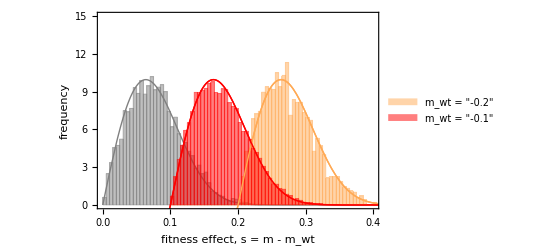

```mathematica
n=4;η=n/2;(*phenotypic dimensions*)
Es=0.01;(*mean mutational selective efffect*)
λ=2Es/n;(*mutational variance, i.e., scaled size*)
uo=0 UnitVector[n,1];(*mean mutational size; set to all zeros*)
U=10^-1;

mmax=0.5; (*max growth rate*)
mwts={(*-0.3,*)-0.2,-0.1};nmwts=Length[mwts];(*wildtype growth rates*)
color={(*Darker[Blue,0.7],*)Lighter[Orange],Red};(*colors*)
zis=Table[√(2(mmax-mwts[[i]]))UnitVector[n,1],{i,nmwts}];(*vector from wildtype from the optimum along trait 1 axis*)

nmuts={(*10^8,*)10^4,10^4};(*number of single mutants to simulate for each mwt*)
(*nmuts={(*10^8,*)10^6,10^6,10^6};*)(*for paper quality figures*)

Rescuems={};
k=1;
While[k<nmwts+1,
m1star=m1/.FindRoot[U p2succ-m1^2/.Subscript[α, 0]->Subscript[α, m1]/.Subscript[β, 0]->Subscript[β, m1]/.Subscript[α, m1]->λ (1+2ϵ)/(1+ϵ)/.Subscript[β, m1]->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax-m1/.λ->2Es/n,{m1,-0.02}];
p2m1=p2succ/.Subscript[α, m1]->λ (1+2ϵ)/(1+ϵ)/.Subscript[β, m1]->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax-m1/.λ->2Es/n;

rescuems={};

dzs=RandomReal[MultinormalDistribution[uo,λ Idn],nmuts[[k]]];(*first mutations*)
ms=mwts[[k]]+ss[dzs,zis[[k]]];(*first mutant growth rates*)
ms=Select[ms,Abs[#]<Abs[m1star]&];(*select only sufficiently critical*)
rv=RandomReal[1,Length[ms]]; (*random uniform in [0,1] for each sufficiently critical mutant*)
keep=Table[rv[[i]]<Exp[-2ms[[i]]],{i,Length[ms]}];(*does mutant itself not establish?*)
who=Position[keep,True];(*which don't establish*)
ms=Extract[ms,who];(*keep those that don't themselves establish*)
rv=RandomReal[1,Length[ms]]; (*random uniform in [0,1] for each sufficiently critical mutant that does not establish*)
keep=Table[rv[[i]]<2 √(U p2m1/.m1->ms[[i]]),{i,Length[ms]}];(*does mutant persist long enough to almost surely rescue?*)
who=Position[keep,True];(*which lead to rescue*)
ms=Extract[ms,who];(*growth rates of first mutants that lead to rescue*)

m2r={};
j=1;
While[j<Length[ms]+1,
zi=√(2(mmax-ms[[j]]))UnitVector[n,1];(*vector from first mutant to optimum*) 

rescued=False;
While[rescued==False,
dz=RandomReal[MultinormalDistribution[uo,λ Idn]];(*second mutations*)
m2=ms[[j]]+ss[{dz},zi][[1]];(*second mutant growth rate*)
rescued=RandomReal[]>Exp[-2m2](*second mutant establish?*)
];

AppendTo[m2r,m2];(*add growth rates of those second mutants that establish*)
j++
];

AppendTo[rescuems,m2r-mwts[[k]]];(*add selection coefficients of those that establish*)

AppendTo[Rescuems,rescuems];
k++
]

styl={FontFamily-> "Times",FontSize->14};(*styles of axes and legend*)
legends=Table[Style[StringForm["m_wt = ``",NumberForm[mwts[[k]],3]],14],{k,nmwts}]; 
simuls=Histogram[Flatten[Rescuems,1],50,"PDF",ChartStyle->color,PlotRange->{{0,mmax-Min[mwts]},All},ChartLegends->Placed[legends,{0.85,0.8}],Axes->False];

Clear[m2]
Table[PmrescueApprox/.α->λ (1+2ϵ)/(1+ϵ)/.β->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax-0/.m->mwts[[i]]+s,{i,nmwts}];
theory=Plot[%,{s,0,mmax-Min[mwts]},PlotStyle->color,PlotRange->All,Frame->{True,True,False,False}];

nmuts={10^5};(*number of mutants to simulate for each mwt*)
mwts={(*-0.3,*)0};nmwts=Length[mwts];(*wildtype growth rates*)
color={(*Darker[Blue,0.7],*)Gray};(*colors*)
zis=Table[√(2(mmax-mwts[[i]]))UnitVector[n,1],{i,nmwts}];
Rescuems={};
k=1;
While[k<nmwts+1,

rescuems={};

dz2=RandomReal[MultinormalDistribution[uo,λ Idn],nmuts[[k]]];(*mutant phenotypes*)
ms=mwts[[k]]+ss[dz2,zis[[k]]];(*mutant growth rates*)
rvs=RandomReal[1,nmuts[[k]]];(*random #*)
fixs=Table[rvs[[i]]<(1-Exp[-2ms[[i]]])1HeavisideTheta[ms[[i]]],{i,nmuts[[k]]}];(*determine if establish*)
Table[If[fixs[[i]],AppendTo[rescuems,ms[[i]]]],{i,Length[ms]}];(*add growth rates of those that establish*)

AppendTo[Rescuems,rescuems];
k++
]
constantsimuls=Histogram[Rescuems,50,"PDF",ChartStyle->color,PlotRange->{{0,mmax-Min[mwts]},All},Axes->False];
Table[PmrescueApprox/.α->λ (1+2ϵ)/(1+ϵ)/.β->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax-mwts[[i]],{i,nmwts}];
constanttheory=Plot[%,{m,0,mmax},PlotStyle->color,PlotRange->All,Frame->{True,True,False,False}];


Show[{constanttheory,constantsimuls,theory,simuls,theory},LabelStyle->styl,Frame->{True,True,False,False},FrameLabel->{Style["fitness effect, s = m - m_wt",14],Style["frequency",14]},PlotRange->{{0,0.4},{0,15}}]
(*Export[imagedir<>"fs2stepCritrescueRealer.pdf",%];*)

Clear[n,λ,mmax,n0,U,k,j,Es]
```

#### Distribution of fitness effects of individual mutations following rescue

We could also consider the pdf of the effects of individual mutations on growth rate. Looking at the effect of individual mutations from 2-step critical rescue on the growth rate of otherwise wildtype individuals we would see some mutations create a growth rate near zero (this is the first step), with individuals varying from -√(U p) to √(U p), and then we would see the effects of the second mutations as well, which could have relatively small improvements in growth rate over the ancestor.

Given a single mutant with slightly subcritical growth rate m1, the rate of critical 2-step rescue through this type is proportional to

```mathematica
√p2succ
```

√(1+(-Gamma[β_m1,mmax/α_m1]+ⅇ^(-2 mmax) Gamma[β_m1,mmax (-2+1/α_m1)] (1-2 α_m1)^-β_m1)/Gamma[β_m1]-ⅇ^(-2 mmax) (1-2 α_m1)^-β_m1)

When this is small it is also proportional to the probability of critical 2-step rescue given m1. The pdf of m1 from the wildtype is roughly

```mathematica
Simplify[PDF[TransformedDistribution[so-γ,γ\[Distributed]GammaDistribution[Subscript[β, mwt],Subscript[α, mwt]]],s],so-s>0]/.so->mmax-mwt/.s->m1-mwt
```

(ⅇ^((m1-mmax)/α_mwt) (-m1+mmax)^(-1+β_mwt) α_mwt^-β_mwt)/Gamma[β_mwt]

We can try to use our approximation of this (needed to normalize by taking integral in denominator). The pdf of slightly subcritical m1 given critical 2-step rescue would then be

```mathematica
Simplify[PDF[TransformedDistribution[so-γ,γ\[Distributed]GammaDistribution[Subscript[β, mwt],Subscript[α, mwt]]],s],so-s>0]/.so->mmax-mwt/.s->m1-mwt;
 %√p2succ/.Subscript[α, m1]->Subscript[α, 0]/.Subscript[β, m1]->Subscript[β, 0];
pm1subcrit=%/Integrate[%,{m1,-a,0},Assumptions->{a>0,mmax>0}]/.a->m1crit0
```

(ⅇ^((m1-mmax)/α_mwt) (-m1+mmax)^(-1+β_mwt) (1/α_mwt)^β_mwt)/(Gamma[β_mwt,mmax/α_mwt]-Gamma[β_mwt,(mmax+√(U (1+(-Gamma[β_0,mmax/α_0]+ⅇ^(-2 mmax) Gamma[β_0,mmax (-2+1/α_0)] (1-2 α_0)^-β_0)/Gamma[β_0]-ⅇ^(-2 mmax) (1-2 α_0)^-β_0)))/α_mwt])

Check the approximation:

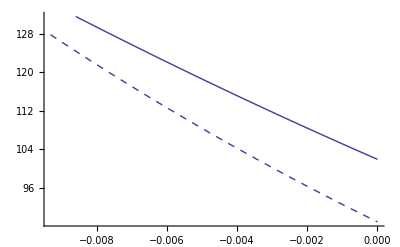

```mathematica
params={Es->0.01,mmax->0.5,n->4,mwt->-0.2,c->-1};

mlim=m1/.FindRoot[U p2succ-m1^2/.U->10^c Uc/.Uc->n^2 λ/4/.Subscript[α, m1]->λ (1+2ϵ)/(1+ϵ)/.Subscript[β, m1]->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax-m1/.λ->2Es/n/.params,{m1,-0.02}];

Simplify[PDF[TransformedDistribution[so-γ,γ\[Distributed]GammaDistribution[Subscript[β, mwt],Subscript[α, mwt]]],s],so-s>0]/.so->mmax-mwt/.s->m1-mwt;
%√p2succ/.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params;
%/NIntegrate[%,{m1,mlim,0}];
real=Plot[%,{m1,mlim,0},PlotRange->{0,All}];

mlimapp=-m1crit0/.U->10^c Uc/.Uc->n^2 λ/4/.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params;

pm1subcrit/.U->10^c Uc/.Uc->n^2 λ/4/.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params;
approx=Plot[%,{m1,mlimapp,0},PlotRange->{0,All},PlotStyle->Dashed];


Show[real,approx,PlotRange->All]
```

The approximation (dashed) does okay when mutation rate is small enough (here up to U~Uc/10; see by changing U above).

Given a single mutant with slightly supercritical growth rate m1, the rate of critical 2-step rescue through this type is proportional to

```mathematica
Exp[-2m1] √p2succ
```

ⅇ^(-2 m1) √(1+(-Gamma[β_m1,mmax/α_m1]+ⅇ^(-2 mmax) Gamma[β_m1,mmax (-2+1/α_m1)] (1-2 α_m1)^-β_m1)/Gamma[β_m1]-ⅇ^(-2 mmax) (1-2 α_m1)^-β_m1)

When this is small it is also proportional the probability of critical 2-step rescue given m1. The pdf of m1 from the wildtype is roughly

```mathematica
Simplify[PDF[TransformedDistribution[so-γ,γ\[Distributed]GammaDistribution[Subscript[β, mwt],Subscript[α, mwt]]],s],so-s>0]/.so->mmax-mwt/.s->m1-mwt
```

(ⅇ^((m1-mmax)/α_mwt) (-m1+mmax)^(-1+β_mwt) α_mwt^-β_mwt)/Gamma[β_mwt]

We can try to use our approximation of this (needed to normalize by taking integral in denominator). The pdf of slightly subcritical m1 given critical 2-step rescue would then be

```mathematica
Simplify[PDF[TransformedDistribution[so-γ,γ\[Distributed]GammaDistribution[Subscript[β, mwt],Subscript[α, mwt]]],s],so-s>0]/.so->mmax-mwt/.s->m1-mwt;
 %Exp[-2m1] √p2succ/.Subscript[α, m1]->Subscript[α, 0]/.Subscript[β, m1]->Subscript[β, 0];
pm1supercrit=%/Integrate[%,{m1,0,a},Assumptions->{mmax>a>0}]/.a->m1crit0
```

(ⅇ^(-2 m1+2 mmax+(m1-mmax)/α_mwt) (-m1+mmax)^(-1+β_mwt) (-2+1/α_mwt)^β_mwt)/(-Gamma[β_mwt,mmax (-2+1/α_mwt)]+Gamma[β_mwt,((-mmax+√(U (1+(-Gamma[β_0,mmax/α_0]+ⅇ^(-2 mmax) Gamma[β_0,mmax (-2+1/α_0)] (1-2 α_0)^-β_0)/Gamma[β_0]-ⅇ^(-2 mmax) (1-2 α_0)^-β_0))) (-1+2 α_mwt))/α_mwt])

Check the approximation:

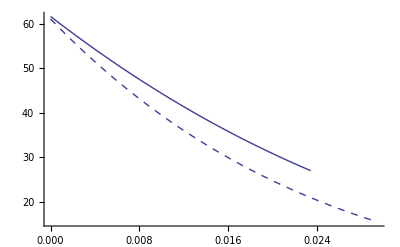

```mathematica
params={Es->0.01,mmax->0.5,n->4,mwt->-0.2,c->0};

mlim=m1/.FindRoot[U p2succ-m1^2/.U->10^c Uc/.Uc->n^2 λ/4/.Subscript[α, m1]->λ (1+2ϵ)/(1+ϵ)/.Subscript[β, m1]->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax-m1/.λ->2Es/n/.params,{m1,-0.02}];

Simplify[PDF[TransformedDistribution[so-γ,γ\[Distributed]GammaDistribution[Subscript[β, mwt],Subscript[α, mwt]]],s],so-s>0]/.so->mmax-mwt/.s->m1-mwt;
%√p2succ/.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params;
%/NIntegrate[%,{m1,0,-mlim}];
real=Plot[%,{m1,0,-mlim},PlotRange->{0,All}];

mlimapp=-m1crit0/.U->10^c Uc/.Uc->n^2 λ/4/.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params;

pm1supercrit/.U->10^c Uc/.Uc->n^2 λ/4/.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params;
approx=Plot[%,{m1,0,-mlimapp},PlotRange->{0,All},PlotStyle->Dashed];


Show[real,approx,PlotRange->All]
```

This full approximation (dashed) does okay for most mutation rates.

OK, so now we can first put this together to get the pdf of m1 given critical 2-step rescue, considering both slightly super and slightly sub critical single mutants.

```mathematica
f=Simplify[PDF[TransformedDistribution[so-γ,γ\[Distributed]GammaDistribution[Subscript[β, mwt],Subscript[α, mwt]]],s],so-s>0]/.so->mmax-mwt/.s->m1-mwt;
pfneg=f √p2succ/.Subscript[α, m1]->Subscript[α, 0]/.Subscript[β, m1]->Subscript[β, 0];
pfnegtot=Integrate[%,{m1,-a,0},Assumptions->{a>0}]/.a->m1crit0;

pfpos=f Exp[-2m1] √p2succ/.Subscript[α, m1]->Subscript[α, 0]/.Subscript[β, m1]->Subscript[β, 0];
pfpostot=Integrate[%,{m1,0,a},Assumptions->{mmax>a>0}]/.a->m1crit0;

pm1negcrit=pfneg/(pfnegtot+pfpostot);
pm1poscrit=pfpos/(pfnegtot+pfpostot);
```

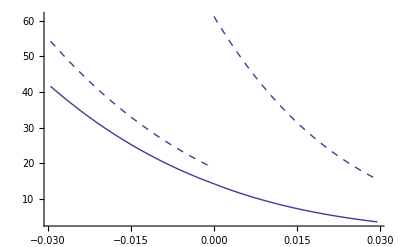

```mathematica
params={Es->0.01,mmax->0.5,n->4,mwt->-0.2,c->0};

mlimapp=-m1crit0/.U->10^c Uc/.Uc->n^2 λ/4/.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params;

pm1subcrit/.U->10^c Uc/.Uc->n^2 λ/4/.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params;
subplt=Plot[%,{m1,mlimapp,0},PlotRange->{0,All},PlotStyle->Dashed];
pm1supercrit/.U->10^c Uc/.Uc->n^2 λ/4/.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params;
superplt=Plot[%,{m1,0,-mlimapp},PlotRange->{0,All},PlotStyle->Dashed];

pm1negcrit/.U->10^c Uc/.Uc->n^2 λ/4/.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params;
negcritplt=Plot[%,{m1,mlimapp,0},PlotRange->{0,All}];
pm1poscrit/.U->10^c Uc/.Uc->n^2 λ/4/.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params;
poscritplt=Plot[%,{m1,0,-mlimapp},PlotRange->{0,All}];

Show[subplt,superplt,negcritplt,poscritplt,PlotRange->All]
```

The dased lines are the pdfs of m1 given 2-step critical rescue by either slightly subcritical or slightly supercritical single mutants. The solid line is the pdf of m1 given 2-step critical rescue (incl both super and sub critical). Note that in this case 2-step critical rescue is more likely through slightly subcritical single mutants (more mutations to this region).

Now we can put together first and second mutations to get the pdf of individual mutation growth rates -- in the wildtype background --  given 2-step critical rescue.

Every 2-step critical rescue event involves two mutations, one near critical first mutation and one second mutation that has a positive growth rate in the first mutant background, but not necessarily in the wildtype background. Therefore the first step mutations should get half the weight and the second step the other half. If these are largely non-overlapping sets of m then we just multiply each by half. But they will often overlap. In that case we want to sum the two in the region of overlap and then add the second mutants outside of that:

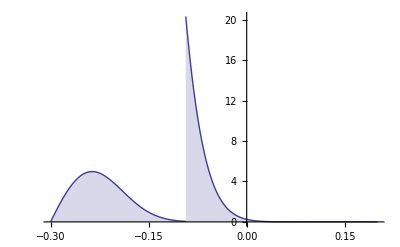

```mathematica
params={Es->0.01,mmax->0.5,n->4,c->1,mwt->-0.3};

pm1wt=PmrescueApprox/.α->λ (1+2ϵ)/(1+ϵ)/.β->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax/.m->m1-mwt/.λ->2Es/n/.params;
mlimapp=-m1crit0/.U->10^c Uc/.Uc->n^2 λ/4/.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params;
part1=(pm1negcrit+pm1wt)/2/.U->10^c Uc/.Uc->n^2 λ/4/.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params;
negcritplt=Plot[%,{m1,mlimapp,0},PlotRange->{0,All},Filling->Bottom];
part2=(pm1poscrit+pm1wt)/2/.U->10^c Uc/.Uc->n^2 λ/4/.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params;
poscritplt=Plot[%,{m1,0,-mlimapp},PlotRange->{0,All},Filling->Bottom];

part3=pm1wt/2/.U->10^c Uc/.Uc->n^2 λ/4/.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params;
negcritplt3=Plot[%,{m1,mwt/.params,mlimapp},PlotRange->{0,All},Filling->Bottom];
part4=pm1wt/2/.U->10^c Uc/.Uc->n^2 λ/4/.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params;
poscritplt4=Plot[%,{m1,-mlimapp,-mwt/.params},PlotRange->{0,All},Filling->Bottom];

(*NIntegrate[part1,{m1,mlimapp,0}]+NIntegrate[part2,{m1,0,-mlimapp}]+NIntegrate[part3,{m1,mwt/.params,mlimapp}]+NIntegrate[part4,{m1,-mlimapp,-mwt/.params}]*)

(*Import[datadir<>"dfem_poisson_N10000_n4_c1.00_Es0.01_mmax0.50_mwt-0.30_mutmax2_nreps10000.csv"]//Flatten;
Select[%,#≠mwts[[1]]&];
data=Histogram[%,20,"PDF",ChartStyle->Directive[Opacity[0.5],color[[1]]]];*)

Show[negcritplt,poscritplt,negcritplt3,poscritplt4,(*data,*)PlotRange->All]
```

### 2-step subcritical

#### Probability of rescue

When the growth rate of the single mutant (m1) is more negative, the logic is only a bit different. Regardless of m1<0, the mutants are effectively critical while the total number is less than -1/m1. And given m1<0 they will almost never grow to sizes greater than -1/m1. Therefore if -√(U p)< m1 <0 then the near critical results above apply as the mutant lineages can persist long enough to reach sizes large enough to spawn a successful rescue mutant. But if  m1<-√(U p) then the mutant lineage cannot reach a size large enough to rescue reliably and the results are different. In this case the mutant will reach a size of at most -1/m1 and persist for at most -1/m1 generations, giving rise to 1/m1^2 individuals. The probability of doing so is -m1, and thus probability a sufficiently subcritical mutant spawns a successful rescue is -1/m1U p.

Altenatively, the expected number of individuals at time t is

```mathematica
D[F[s,t]/.fst,s]/.λ->(1+m)/2/.μ->(1-m)/2/.N0->1//FullSimplify;
Limit[%,s->1]
```

ⅇ^(m t)

Summing over all time, the cumulative expected number of individuals is approximately

```mathematica
D[F[s,t]/.fst,s]/.λ->(1+m)/2/.μ->(1-m)/2/.N0->1//FullSimplify;
Limit[%,s->1];
Sum[%,{t,0,∞}];
Series[%,{m,0,-1}]//Normal
```

-1/m

Either way, the probability a sufficiently subcritical mutant spawns a successful rescue is -1/m1U p.

 In FGM this is roughly

```mathematica
p12del=-U/m1 p2succ
```

-(U (1+(-Gamma[β_m1,mmax/α_m1]+ⅇ^(-2 mmax) Gamma[β_m1,mmax (-2+1/α_m1)] (1-2 α_m1)^-β_m1)/Gamma[β_m1]-ⅇ^(-2 mmax) (1-2 α_m1)^-β_m1))/m1

The rate of 2-step rescue given a sufficiently subcritical single mutant of growth rate m1 is then

```mathematica
Simplify[PDF[TransformedDistribution[so-γ,γ\[Distributed]GammaDistribution[β,α]],s],so-s>0]/.so->mmax-mwt/.s->m1-mwt/.α->Subscript[α, mwt]/.β->Subscript[β, mwt];
rdel2stepm1=p12del %
```

-(ⅇ^((m1-mmax)/α_mwt) (-m1+mmax)^(-1+β_mwt) U (1+(-Gamma[β_m1,mmax/α_m1]+ⅇ^(-2 mmax) Gamma[β_m1,mmax (-2+1/α_m1)] (1-2 α_m1)^-β_m1)/Gamma[β_m1]-ⅇ^(-2 mmax) (1-2 α_m1)^-β_m1) α_mwt^-β_mwt)/(m1 Gamma[β_mwt])

As a function of m1 this looks like

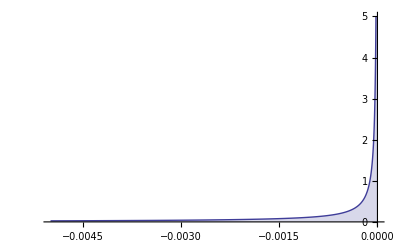

```mathematica
params={Es->0.01, n->4 , mmax->0.5,U->10^0 Uc,mwt->-0.2};
rdel2stepm1 /.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params/.Uc->n^2 λ/4/.λ->2Es/n/.params;
Plot[%,{m1,-0.005,0},PlotRange->{0,5},Filling->Bottom]
```

Using m1 threshold between sufficiently critical and subcritical we can numerically integrate over sufficiently subcritical m1 to get the probability of 2step subcritical rescue

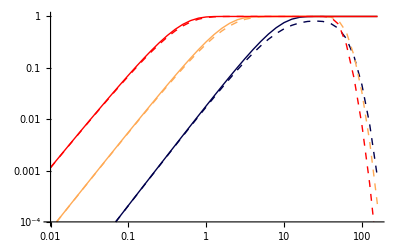

```mathematica
mwts={-0.3,-0.2,-0.1};nmwts=Length[mwts];
color={Darker[Blue,0.7],Lighter[Orange],Red};(*colors*)
colordashed={{Darker[Blue,0.7],Dashed},{Lighter[Orange],Dashed},{Red,Dashed}};(*colors*)
params={Es->0.01, n->4 , mmax->0.5,n0->10^4,U->10^c Uc};
limit=m1crit0/.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params/.Uc->n^2 λ/4/.λ->2Es/n/.params;
r12=(n0 U)/(1-Exp[mwt])rdel2stepm1/.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params/.Uc->n^2 λ/4/.λ->2Es/n/.params;

Table[{10^c,1-Exp[-NIntegrate[r12/.mwt->mwts[[i]],{m1,-∞,-limit}]]},{i,nmwts},{c,-2,2.2,0.1}];

applimplt=ListLogLogPlot[%,Joined->True,PlotStyle->colordashed,PlotRange->{10^-4,All}];
reallimeqn=U p2succ-m1^2/.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params/.Uc->n^2 λ/4/.λ->2Es/n/.params;
Table[{10^c,1-Exp[-NIntegrate[r12/.mwt->mwts[[i]],{m1,-∞,m1/.FindRoot[reallimeqn,{m1,-0.02}]}]]},{i,nmwts},{c,-2,2.2,0.1}];

reallimplt=ListLogLogPlot[%,Joined->True,PlotStyle->color,PlotRange->{10^-4,All}];

Show[applimplt,reallimplt]
```

We see our zeroth order approximation of the integration limit (dashed) produces some funny results for very high mutation rates (compared with the true m1 threshold, obtained numerically and shown in solid). With high mutation rates this approximation greatly overestimates how subcritical a sufficiently critical mutant can be, as increased mutation means shorter required persistence times and the approximation does not incorporate the lower probability a subcritical mutant has in producing a double mutant with sufficiently supercritical growth rate to rescue the population. We thus over-reduce the range of m1 we integrate over for the subcritical path, reducing its probability of occuring.

Lets take a look at the threshold m1 (solid) and its zeroth order approximation (dashed):

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

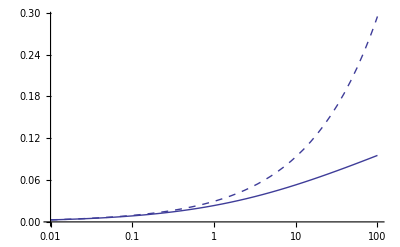

```mathematica
mwts={-0.3,-0.2,-0.1};nmwts=Length[mwts];
color={Darker[Blue,0.7],Lighter[Orange],Red};(*colors*)
colordashed={{Darker[Blue,0.7],Dashed},{Lighter[Orange],Dashed},{Red,Dashed}};(*colors*)
params={Es->0.01, n->4 , mmax->0.5,n0->10^4,U->c Uc};
limit=m1crit0/.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params/.Uc->n^2 λ/4/.λ->2Es/n/.params;

applimplt=LogLinearPlot[limit,{c,10^-2,10^2},PlotStyle->Dashed];
reallimeqn=U p2succ-m1^2/.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params/.Uc->n^2 λ/4/.λ->2Es/n/.params;
Table[{10^y,-m1/.FindRoot[reallimeqn/.c->10^y,{m1,-0.1}]},{y,-2,2,0.1}];

reallimplt=ListLogLinearPlot[%,Joined->True];

Show[applimplt,reallimplt]
```

As we can see, both continue to increase with mutation rate (high mutation rates broaden the range of sufficiently critical because the necessary persistence time drops), but the approximation increases much too fast. We will have to use the numeric solution for m1 or restrict our predictions to small mutation rates.

#### Distribution of fitness effects of rescue genotypes following rescue

Given that 2-step rescue occurs through a sufficiently subcritical single mutant (m1<0), the distribution of the rescue mutant growth rates (that is, individual growth rates) is roughly 
f(m_2 | subcritical 2-step rescue) = ((∫^(m1^*))_(-∞)f(m_1 | m_wt)P(mutant with m_1 mutates)f(m_2| m_1)  P(2-step subcritical rescue| m_2)dm_1)/(P(subcritical 2-step rescue))=((∫^(m1^*))_(-∞)f(m_1 | m_wt)(U/m_1)f(m_2| m_1)  p_est(m_2)dm_1)/(P( 2-step subcritical rescue)).

The numerator is proportional to the integral of

```mathematica
Simplify[PDF[TransformedDistribution[so-γ,γ\[Distributed]GammaDistribution[β,α]],s],so-s>0]/.so->mmax-mwt/.s->m1-mwt/.α->Subscript[α, mwt]/.β->Subscript[β, mwt];
Simplify[PDF[TransformedDistribution[so-γ,γ\[Distributed]GammaDistribution[β,α]],s],so-s>0]/.so->mmax-m1/.s->m2-m1/.α->Subscript[α, m1]/.β->Subscript[β, m1];
pm2m1rescue=%%*1/-m1*%*(1-Exp[-2m2])/Subscript[α, mwt]^(-Subscript[β, mwt])*Gamma[Subscript[β, mwt]]
```

-(ⅇ^((m2-mmax)/α_m1+(m1-mmax)/α_mwt) (1-ⅇ^(-2 m2)) (-m1+mmax)^(-1+β_mwt) (-m2+mmax)^(-1+β_m1) α_m1^-β_m1)/(m1 Gamma[β_m1])

over m1 from -∞ to the critical m1. Both the numerator and denominator (integral over positive m2) will need to be numerically evaluated until we develop a decent analytical prediction. Doing so gives the expected distribution of m

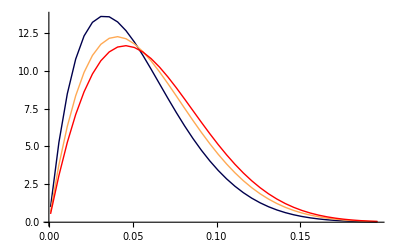

```mathematica
mwts={-0.3,-0.2,-0.1};nmwts=Length[mwts];(*wildtype growth rates*)
color={Darker[Blue,0.7],Lighter[Orange],Red};(*colors*)
params={Es->0.01,mmax->0.5,n->4,n0->10^4,c->-2};

mlim=-m1crit0/.U->10^c/.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params;
pm2m1rescue/.U->10^c /.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params;
Table[
{m2,NIntegrate[%/.mwt->mwts[[i]],{m1,-∞,mlim}]/NIntegrate[%/.mwt->mwts[[i]],{m1,-1,mlim},{m2,0,mmax/.params}]},
{i,nmwts},{m2,0.001,0.2,0.005}];
ListPlot[%,PlotStyle->color,Joined->True,PlotRange->{{0,0.2},{0,All}}]
```

Lets compare to mutants simulated according to (∫^(m1^*))_(-∞)f(m_1 | m_wt)(-U/m_1)f(m_2| m_1)  p_est(m_2)dm_1

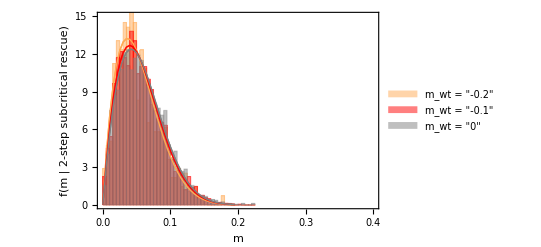

```mathematica
n=4;η=n/2;(*phenotypic dimensions*)
Es=0.01;(*mean mutational selective efffect*)
λ=2Es/n;(*mutational variance, i.e., scaled size*)
uo=0 UnitVector[n,1];(*mean mutational size; set to all zeros*)
U=10^-1;

mmax=0.5; (*max growth rate*)
mwts={(*-0.3,*)-0.2,-0.1};nmwts=Length[mwts];(*wildtype growth rates*)
color={(*Darker[Blue,0.7],*)Lighter[Orange],Red};(*colors*)
zis=Table[√(2(mmax-mwts[[i]]))UnitVector[n,1],{i,nmwts}];(*vector from wildtype from the optimum along trait 1 axis*)

(*nmuts={(*10^8,*)10^6,10^6,10^6};*)(*for paper quality figures*)
nmuts={(*10^8,*)10^4,10^4};(*number of single mutants to simulate for each mwt*)

Rescuems={};
k=1;
While[k<nmwts+1,

m1star=m1/.FindRoot[U p2succ-m1^2/.Subscript[α, 0]->Subscript[α, m1]/.Subscript[β, 0]->Subscript[β, m1]/.Subscript[α, m1]->λ (1+2ϵ)/(1+ϵ)/.Subscript[β, m1]->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax-m1/.λ->2Es/n/.params,{m1,-0.02}];

rescuems={};

dz1=RandomReal[MultinormalDistribution[uo,λ Idn],nmuts[[k]]];(*first mutations*)
ms1=mwts[[k]]+ss[dz1,zis[[k]]];(*single mutant growth rates*)
ms1sub=Select[ms1,#<m1star&];(*select only sufficiently subcritical*)
ndm=Table[RandomVariate[PoissonDistribution[-U/ms1sub[[i]]]],{i,Length[ms1sub]}]; (*number of double mutants produced by each single mutant*)
who=Position[ndm,_?(#>0&)];(*who created at least 1 double mutant?*)
ms1mut=Extract[ms1sub,who];(*keep only those that produced double mutant*)
ndm=Select[ndm,#>0&];
dz2=Table[RandomReal[MultinormalDistribution[uo,λ Idn],ndm[[i]]],{i,Length[ms1mut]}];(*second mutations*)
zis1=Table[√(2(mmax-ms1sub[[i]]))UnitVector[n,1],{i,Length[ms1mut]}];
ms2=Table[ms1sub[[i]]+ss[dz2[[i]],zis1[[i]]],{i,Length[ms1mut]}]//Flatten;(*double mutant growth rates*)
rvs=RandomReal[1,Total[ndm]];(*random # for each double mutant*)
fixs=Table[rvs[[i]]<(1-Exp[-2ms2[[i]]])1HeavisideTheta[ms2[[i]]],{i,Total[ndm]}];(*determine if establish*)
Table[If[fixs[[i]],AppendTo[rescuems,ms2[[i]]]],{i,Total[ndm]}];(*add growth rates of those that establish*)

AppendTo[Rescuems,rescuems];
k++
]


legends=Table[Style[StringForm["m_wt = ``",NumberForm[mwts[[k]],3]],14],{k,nmwts}]; 
simuls=Histogram[Rescuems,50,"PDF",ChartStyle->color,PlotRange->{{0,mmax},All},ChartLegends->Placed[legends,{0.85,0.8}],Axes->False];

m1star=m1/.FindRoot[U p2succ-m1^2/.Subscript[α, 0]->Subscript[α, m1]/.Subscript[β, 0]->Subscript[β, m1]/.Subscript[α, m1]->λ (1+2ϵ)/(1+ϵ)/.Subscript[β, m1]->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax-m1/.λ->2Es/n/.params,{m1,-0.02}];
pm2m1rescue/.U->10^c /.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params;
Table[
{m2,NIntegrate[%/.mwt->mwts[[i]],{m1,-∞,m1star}]/NIntegrate[%/.mwt->mwts[[i]],{m1,-1,m1star},{m2,0,mmax/.params}]},
{i,nmwts},{m2,0.0001,0.2,0.005}];
theory=ListPlot[%,PlotStyle->color,Joined->True,PlotRange->{{0,0.25},{0,All}}];

Show[{theory,simuls,theory},LabelStyle->styl,Frame->{True,True,False,False},FrameLabel->{Style["m",14],Style["f(m | 2-step subcritical rescue)",14]},PlotRange->{{0,0.25},{0,15}}]
(*Export[imagedir<>"fm2stepSubrescue.pdf",%];*)

Clear[n,λ,mmax,n0,U,k,j,Es]
```

in terms of s:

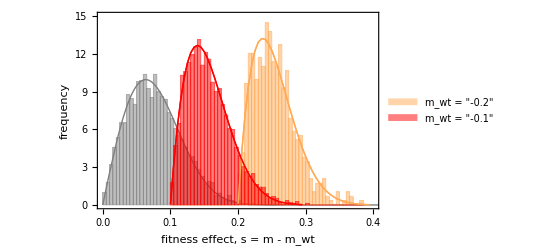

```mathematica
n=4;η=n/2;(*phenotypic dimensions*)
Es=0.01;(*mean mutational selective efffect*)
λ=2Es/n;(*mutational variance, i.e., scaled size*)
uo=0 UnitVector[n,1];(*mean mutational size; set to all zeros*)
U=10^-1;

mmax=0.5; (*max growth rate*)
mwts={(*-0.3,*)-0.2,-0.1};nmwts=Length[mwts];(*wildtype growth rates*)
color={(*Darker[Blue,0.7],*)Lighter[Orange],Red};(*colors*)
zis=Table[√(2(mmax-mwts[[i]]))UnitVector[n,1],{i,nmwts}];(*vector from wildtype from the optimum along trait 1 axis*)

nmuts={(*10^8,*)10^4,10^4};(*number of single mutants to simulate for each mwt*)
(*nmuts={(*10^8,*)10^6,10^6};*)(*for paper quality figures*)

Rescuems={};
k=1;
While[k<nmwts+1,

m1star=m1/.FindRoot[U p2succ-m1^2/.Subscript[α, 0]->Subscript[α, m1]/.Subscript[β, 0]->Subscript[β, m1]/.Subscript[α, m1]->λ (1+2ϵ)/(1+ϵ)/.Subscript[β, m1]->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax-m1/.λ->2Es/n/.params,{m1,-0.02}];

rescuems={};

dz1=RandomReal[MultinormalDistribution[uo,λ Idn],nmuts[[k]]];(*first mutations*)
ms1=mwts[[k]]+ss[dz1,zis[[k]]];(*single mutant growth rates*)
ms1sub=Select[ms1,#<m1star&];(*select only sufficiently subcritical*)
ndm=Table[RandomVariate[PoissonDistribution[-U/ms1sub[[i]]]],{i,Length[ms1sub]}]; (*number of double mutants produced by each single mutant*)
who=Position[ndm,_?(#>0&)];(*who created at least 1 double mutant?*)
ms1mut=Extract[ms1sub,who];(*keep only those that produced double mutant*)
ndm=Select[ndm,#>0&];
dz2=Table[RandomReal[MultinormalDistribution[uo,λ Idn],ndm[[i]]],{i,Length[ms1mut]}];(*second mutations*)
zis1=Table[√(2(mmax-ms1sub[[i]]))UnitVector[n,1],{i,Length[ms1mut]}];
ms2=Table[ms1sub[[i]]+ss[dz2[[i]],zis1[[i]]],{i,Length[ms1mut]}]//Flatten;(*double mutant growth rates*)
rvs=RandomReal[1,Total[ndm]];(*random # for each double mutant*)
fixs=Table[rvs[[i]]<(1-Exp[-2ms2[[i]]])1HeavisideTheta[ms2[[i]]],{i,Total[ndm]}];(*determine if establish*)
Table[If[fixs[[i]],AppendTo[rescuems,ms2[[i]]-mwts[[k]]]],{i,Total[ndm]}];(*add growth rates of those that establish*)

AppendTo[Rescuems,rescuems];
k++
]


legends=Table[Style[StringForm["m_wt = ``",NumberForm[mwts[[k]],3]],14],{k,nmwts}]; 
simuls=Histogram[Rescuems,50,"PDF",ChartStyle->color,PlotRange->{{0,mmax-Min[mwts]},All},ChartLegends->Placed[legends,{0.85,0.8}],Axes->False];

m1star=m1/.FindRoot[U p2succ-m1^2/.Subscript[α, 0]->Subscript[α, m1]/.Subscript[β, 0]->Subscript[β, m1]/.Subscript[α, m1]->λ (1+2ϵ)/(1+ϵ)/.Subscript[β, m1]->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax-m1/.λ->2Es/n/.params,{m1,-0.02}];
pm2m1rescue/.U->10^c /.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params;
Table[
{m2-mwts[[i]],NIntegrate[%/.mwt->mwts[[i]],{m1,-∞,m1star}]/NIntegrate[%/.mwt->mwts[[i]],{m1,-1,m1star},{m2,0,mmax/.params}]},
{i,nmwts},{m2,0.0001,0.2,0.005}];
theory=ListPlot[%,PlotStyle->color,Joined->True,PlotRange->{{0,0.5},{0,All}}];

nmuts={10^5};(*number of mutants to simulate for each mwt*)
mwts={(*-0.3,*)0};nmwts=Length[mwts];(*wildtype growth rates*)
color={(*Darker[Blue,0.7],*)Gray};(*colors*)
zis=Table[√(2(mmax-mwts[[i]]))UnitVector[n,1],{i,nmwts}];
Rescuems={};
k=1;
While[k<nmwts+1,

rescuems={};

dz2=RandomReal[MultinormalDistribution[uo,λ Idn],nmuts[[k]]];(*mutant phenotypes*)
ms=mwts[[k]]+ss[dz2,zis[[k]]];(*mutant growth rates*)
rvs=RandomReal[1,nmuts[[k]]];(*random #*)
fixs=Table[rvs[[i]]<(1-Exp[-2ms[[i]]])1HeavisideTheta[ms[[i]]],{i,nmuts[[k]]}];(*determine if establish*)
Table[If[fixs[[i]],AppendTo[rescuems,ms[[i]]]],{i,Length[ms]}];(*add growth rates of those that establish*)

AppendTo[Rescuems,rescuems];
k++
]
constantsimuls=Histogram[Rescuems,50,"PDF",ChartStyle->color,PlotRange->{{0,mmax-Min[mwts]},All},Axes->False];
Table[PmrescueApprox/.α->λ (1+2ϵ)/(1+ϵ)/.β->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax-mwts[[i]],{i,nmwts}];
constanttheory=Plot[%,{m,0,mmax},PlotStyle->color,PlotRange->All,Frame->{True,True,False,False}];

Show[{constanttheory,constantsimuls,theory,simuls,theory},LabelStyle->styl,Frame->{True,True,False,False},FrameLabel->{Style["fitness effect, s = m - m_wt",14],Style["frequency",14]},PlotRange->{{0,0.4},{0,15}}]
(*Export[imagedir<>"fs2stepSubrescue.pdf",%];*)

Clear[n,λ,mmax,n0,U,k,j,Es]
```

Note that there are very slight differences depending on stress (m_wt), as this affects what m_1 will appear (and hence what m_2 are likely to appear). Because wildtypes with more negative growth rates are likely to produce more subcritical single mutants, the double mutants that rescue those populations have growth rates more clustered around small positive growth rates just above 1, reducing the variance. Less stressed wildtypes can produce more fit single mutants, which can produce more fit double mutants, widening the variance.

#### Distribution of fitness effects of individual mutations following rescue

Given that 2-step rescue occurs through a sufficiently subcritical single mutant (m1<0), the distribution of the subctritical (first step mutation) growth rates is roughly f(m_1 | critical 2-step rescue) = (f(m_1| m_wt)  P(2-step subcritical rescue| m1))/(P(subcritical 2-step rescue)).

The numerator is proportional to

```mathematica
Simplify[PDF[TransformedDistribution[so-γ,γ\[Distributed]GammaDistribution[β,α]],s],so-s>0]/.so->mmax-mwt/.s->m1-mwt/.α->Subscript[α, mwt]/.β->Subscript[β, mwt];
pm1rescuesubcrit=p2succ/m1%/-Subscript[α, mwt]^(-Subscript[β, mwt])*Gamma[Subscript[β, mwt]]
```

-(ⅇ^((m1-mmax)/α_mwt) (-m1+mmax)^(-1+β_mwt) (1+(-Gamma[β_m1,mmax/α_m1]+ⅇ^(-2 mmax) Gamma[β_m1,mmax (-2+1/α_m1)] (1-2 α_m1)^-β_m1)/Gamma[β_m1]-ⅇ^(-2 mmax) (1-2 α_m1)^-β_m1))/m1

The denominator we will need to deal with numerically until we find a decent approximation.

So the distribution of the first mutation in 2-step subcritical rescue looks something like

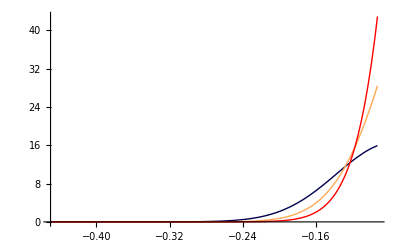

```mathematica
mwts={-0.3,-0.2,-0.1};nmwts=Length[mwts];(*wildtype growth rates*)
color={Darker[Blue,0.7],Lighter[Orange],Red};(*colors*)
params={Es->0.01,mmax->0.5,n->4,n0->10^4,c->1};

mlim=-m1crit0/.U->10^c Uc/.Uc->n^2 λ/4/.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params;
pm1rescuesubcrit/.U->10^c Uc/.Uc->n^2 λ/4/.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params;
Table[%/NIntegrate[%/.mwt->mwts[[i]],{m1,-∞,mlim}]/.mwt->mwts[[i]],{i,nmwts}];

Plot[%,{m1,-0.45,mlim},PlotRange->All,PlotStyle->color]
```

### Comparing critical vs subcritical 2-step rescue

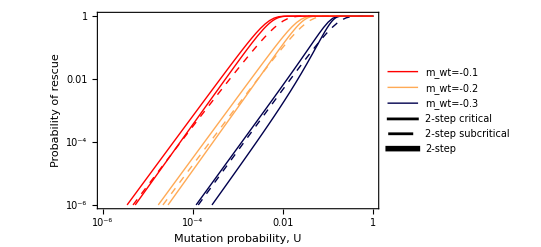

```mathematica
mwts={-0.3,-0.2,-0.1};nmwts=Length[mwts];(*wildtype growth rates*)
color={Darker[Blue,0.7],Lighter[Orange],Red};(*colors*)
colordashed={{Darker[Blue,0.7],Dashed},{Lighter[Orange],Dashed},{Red,Dashed}};(*colors*)
colorthick={Directive[Darker[Blue,0.7],Thick],Directive[Lighter[Orange],Thick],Directive[Red,Thick]};(*colors*)
params={Es->0.01,mmax->0.5,n->4,n0->10^4};
nint=1;
(*nint=0.1;*)(*publication quality*)
rate2=((n0 U)/(1-Exp[mwt]))criticalrate/.a->m1crit0 /.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params;

Table[1-Exp[-rate2]/.mwt->mwts[[i]],{i,nmwts}];
twostepcrit=LogLogPlot[%,{U,10^-6,10^0},PlotStyle->color,PlotRange->{10^-6,All},Frame->{True,True,False,False}];

r12=((n0 U)/(1-Exp[mwt]))rdel2stepm1/.U->10^c /.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params;
reallimeqn=U p2succ-m1^2/.U->10^c /.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params;
Table[{10^c,1-Exp[-NIntegrate[r12/.mwt->mwts[[i]],{m1,-∞,m1/.FindRoot[reallimeqn,{m1,-0.02}]}]]/.mwt->mwts[[i]]},{i,nmwts},{c,-6,0,nint}];
twostepsub=ListLogLogPlot[%,Joined->True,PlotStyle->colordashed,PlotRange->{10^-6,All},Frame->{True,True,False,False}];


rate2/.U->10^c;
Table[{10^c,1-Exp[-%-NIntegrate[r12/.mwt->mwts[[i]],{m1,-∞,m1/.FindRoot[reallimeqn,{m1,-0.02}]}]]/.mwt->mwts[[i]]},{i,nmwts},{c,-6,0,nint}];
twostep=ListLogLogPlot[%,Joined->True,PlotStyle->colorthick,PlotRange->{10^-6,All},Frame->{True,True,False,False}];

Legended[
Show[
twostepcrit,
twostepsub,
twostep,
FrameStyle->Directive[14],
FrameLabel->{Style["Mutation probability, U",14],Style["Probability of rescue",14]},
(*ImageSize->500,*)
PlotRangePadding->None
],
{
Placed[
LineLegend[{Directive[Black,Thickness[0.1]],Directive[Dashing[Medium],Thickness[0.1]],Directive[Thickness[0.2]]},{Style["2-step critical",14],Style["2-step subcritical",14],Style["2-step",14]},LegendLayout->"Row"],
Top],
Placed[
LineLegend[Reverse[colorthick],{Style["m_wt=-0.1",14],Style["m_wt=-0.2",14],Style[ "m_wt=-0.3",14]},LegendLayout->"Column"],
Scaled@{0.2,0.8}]
}
]

(*rasterTrick[%]*)
(*Export[imagedir<>"2stepCritvsSub.pdf",%];*)
```

## (a+b) Comparing and combining 1-step and 2-step pathways

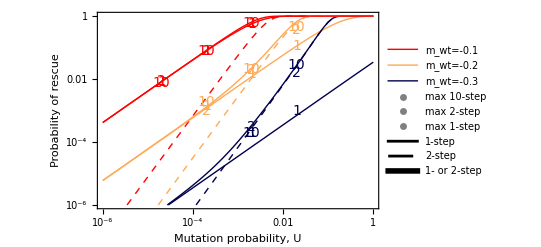

```mathematica
mwts={-0.3,-0.2,-0.1};nmwts=Length[mwts];(*wildtype growth rates*)
color={Darker[Blue,0.7],Lighter[Orange],Red};(*colors*)
colordashed={{Darker[Blue,0.7],Dashed},{Lighter[Orange],Dashed},{Red,Dashed}};(*colors*)
colorthick={Directive[Darker[Blue,0.7],Thick],Directive[Lighter[Orange],Thick],Directive[Red,Thick]};(*colors*)
params={Es->0.01,mmax->0.5,n->4,n0->10^4};
nint=1;
(*nint=0.1;*)(*publication quality*)

r12=((n0 U)/(1-Exp[mwt]))rdel2stepm1/.U->10^c /.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params;
reallimeqn=U p2succ-m1^2/.U->10^c /.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params;

rate2=((n0 U)/(1-Exp[mwt]))criticalrate/.a->m1crit0/.U->10^c/.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params;

Table[{10^c,1-Exp[-rate2-NIntegrate[r12/.mwt->mwts[[i]],{m1,-∞,m1/.FindRoot[reallimeqn,{m1,-0.02}]}]]/.mwt->mwts[[i]]},{i,nmwts},{c,-6,0,nint}];
twostep=ListLogLogPlot[%,Joined->True,PlotStyle->colordashed,PlotRange->{10^-6,All},Frame->{True,True,False,False}];

rate1=((n0 U)/(1-Exp[mwt]))(1+(ⅇ^(-2 mmax) (1-2 α)^-β (-Gamma[β]+Gamma[β,mmax (-2+1/α)]))/Gamma[β]-Gamma[β,mmax/α]/Gamma[β])/.U->c /.α->λ (1+2ϵ)/(1+ϵ)/.β->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax-mwt/.λ->2Es/n/.params;
Table[1-Exp[-rate1]/.mwt->mwts[[i]],{i,nmwts}];

onestep=LogLogPlot[%,{c,10^-6,10^0},PlotStyle->color,PlotRange->{10^-6,1},Frame->{True,True,False,False}];

rate1/.c->10^c;
Table[{10^c,1-Exp[-%-rate2-NIntegrate[r12/.mwt->mwts[[i]],{m1,-∞,m1/.FindRoot[reallimeqn,{m1,-0.02}]}]]/.mwt->mwts[[i]]},{i,nmwts},{c,-6,0,nint}];
allstepplt=ListLogLogPlot[%,Joined->True,PlotStyle->colorthick,PlotRange->{10^-6,All},Frame->{True,True,False,False}];

Import[datadir<>"prescue_poisson_N10000_n4_Es0.01_mmax0.50_mwt-0.10_nreps10000.csv"];
dat=Table[Select[%,#[[2]]==i&][[All,{1,3}]],{i,{1,2,10}}];
dat[[All,All,{1}]]=dat[[All,All,{1}]]*Uc/.Uc->n^2 λ/4/.λ->2Es/n/.params;data1=ListLogLogPlot[dat,PlotMarkers->{Style["1",14],Style["2",14],Style["10",14]},PlotStyle->{{color[[3]],PointSize[Large]},{color[[3]],PointSize[Large]},{color[[3]],PointSize[Large]}}];

Import[datadir<>"prescue_poisson_N10000_n4_Es0.01_mmax0.50_mwt-0.20_nreps10000.csv"];
dat=Table[Select[%,#[[2]]==i&][[All,{1,3}]],{i,{1,2,10}}];
dat[[All,All,{1}]]=dat[[All,All,{1}]]*Uc/.Uc->n^2 λ/4/.λ->2Es/n/.params;data2=ListLogLogPlot[dat,PlotMarkers->{Style["1",14],Style["2",14],Style["10",14]},PlotStyle->{{color[[2]],PointSize[Large]},{color[[2]],PointSize[Large]},{color[[2]],PointSize[Large]}}];

Import[datadir<>"prescue_poisson_N10000_n4_Es0.01_mmax0.50_mwt-0.30_nreps10000.csv"];
dat=Table[Select[%,#[[2]]==i&][[All,{1,3}]],{i,{1,2,10}}];
dat[[All,All,{1}]]=dat[[All,All,{1}]]*Uc/.Uc->n^2 λ/4/.λ->2Es/n/.params;data3=ListLogLogPlot[dat,PlotMarkers->{Style["1",14],Style["2",14],Style["10",14]},PlotStyle->{{color[[1]],PointSize[Large]},{color[[1]],PointSize[Large]},{color[[1]],PointSize[Large]}}];

Legended[
Show[
twostep,
onestep,
allstepplt,
data1,
data2,
data3,
FrameStyle->Directive[14],
FrameLabel->{Style["Mutation probability, U",14],Style["Probability of rescue",14]},
ImageSize->400,
PlotRangePadding->None
],
{
Placed[
LineLegend[{Directive[Black,Thickness[0.1]],Directive[Dashing[Medium],Thickness[0.1]],Directive[Thickness[0.2]]},{Style["1-step",14],Style["2-step",14],Style["1- or 2-step",14]},LegendLayout->"Row"],
Top],
Placed[
LineLegend[Reverse[colorthick],{Style["m_wt=-0.1",14],Style["m_wt=-0.2",14],Style[ "m_wt=-0.3",14]},LegendLayout->"Column"],
Scaled@{0.15,0.85}],
Placed[
PointLegend[{Gray,Gray,Gray},{Style["max 10-step",14],Style["max 2-step",14], Style["max 1-step",14]},LegendMarkers->{Style["10",14],Style["2",14],Style["1",14]},LegendLayout->"Column",LegendLabel->Style["Simulations",14,Underlined]],
Scaled@{0.85,0.25}]
}
]

(*rasterTrick[%]*)
(*Export[imagedir<>"1or2stepRescueSimp.pdf",%];*)
```

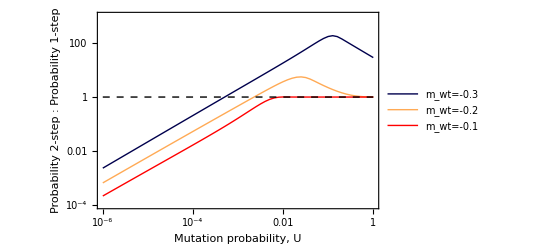

```mathematica
mwts={-0.3,-0.2,-0.1};nmwts=Length[mwts];(*wildtype growth rates*)
color={Darker[Blue,0.7],Lighter[Orange],Red};(*colors*)
colordashed={{Darker[Blue,0.7],Dashed},{Lighter[Orange],Dashed},{Red,Dashed}};(*colors*)
colorthick={Directive[Darker[Blue,0.7],Thick],Directive[Lighter[Orange],Thick],Directive[Red,Thick]};(*colors*)
params={Es->0.01,mmax->0.5,n->4,n0->10^4};
nint=1;
(*nint=0.1;*)(*publication quality*)

mlim=m1crit0/.U->10^c /.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params;
rate2sub=((n0 U)/(1-Exp[mwt]))rdel2stepm1/.U->10^c/.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params;
rate2crit=((n0 U)/(1-Exp[mwt]))criticalrate/.a->m1crit0/.U->10^c /.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params;

rate1=((n0 U)/(1-Exp[mwt]))(1+(ⅇ^(-2 mmax) (1-2 α)^-β (-Gamma[β]+Gamma[β,mmax (-2+1/α)]))/Gamma[β]-Gamma[β,mmax/α]/Gamma[β])/.U->10^c/.α->λ (1+2ϵ)/(1+ϵ)/.β->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax-mwt/.λ->2Es/n/.params;


Table[{10^c,(1-Exp[-(rate2crit+NIntegrate[rate2sub/.mwt->mwts[[i]],{m1,-∞,-mlim}])])/(1-Exp[-rate1])/.mwt->mwts[[i]]},{i,nmwts},{c,-6,0,nint}];
plot=ListLogLogPlot[%,Joined->True,PlotStyle->colorthick,PlotRange->{10^-4,10^3},Frame->{True,True,False,False}];


Legended[
Show[
plot,
LogLogPlot[1,{c,10^-6,10^0},PlotStyle->{Black,Dashed}],
FrameStyle->Directive[14],
FrameLabel->{Style["Mutation probability, U",14],Style["Probability 2-step : Probability 1-step",14]},
ImageSize->400,
PlotRangePadding->None
],
{
Placed[
LineLegend[colorthick,{Style["m_wt=-0.3",14],Style["m_wt=-0.2",14],Style[ "m_wt=-0.1",14]},LegendLayout->"Column"],
Scaled@{0.85,0.25}]
}
]

(*rasterTrick[%]*)
(*Export[imagedir<>"2to1ratioRescueSimp.pdf",%];*)
```

## (a+b) Inferring the genetic pathway to rescue

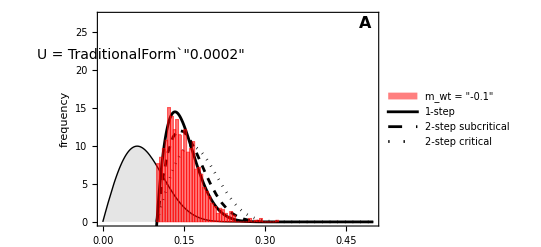

```mathematica
dat=Import[datadir<>"dfe_poisson_N10000_n4_c0.01_Es0.01_mmax0.50_mwt-0.10_mutmax10_nreps10000.csv"];
mwtchoice=3;
params={n->4,Es->0.01, mmax->0.5,c->0.01};
nint=0.01;
letter=Style["A",16,Bold];

allmwts={-0.3,-0.2,-0.1};
mwts={allmwts[[mwtchoice]]};nmwts=Length[mwts];
legends=Table[Style[StringForm["m_wt = ``",NumberForm[mwts[[i]],3]],14],{i,nmwts}]; 
allcolors={Darker[Blue,0.7],Lighter[Orange],Red};
chartcolor={allcolors[[mwtchoice]]};
color=Directive[Black,Thickness[0.005]];(*colors*)
colordashed=Directive[Black,Dashed,Thickness[0.005]];(*colors*)
colordotted=Directive[Black,Dotted,Thickness[0.005]];(*colors*)
styl={FontFamily->"Times",FontSize->14};
mutlab=Style[StringForm["U = ``",NumberForm[c n^2 λ/4/.λ->2Es/n/.params,1]],14];

(ⅇ^((m-mmax)/α) (1-ⅇ^(-2 m)) (-m+mmax)^(-1+β) α^-β)/(Gamma[β] (1+(ⅇ^(-2 mmax) (1-2 α)^-β (-Gamma[β]+Gamma[β,mmax (-2+1/α)]))/Gamma[β]-Gamma[β,mmax/α]/Gamma[β]))/.α->λ (1+2ϵ)/(1+ϵ)/.β->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax-mwt/.λ->2Es/n/.params;
theory0step=Plot[%/.m->s+mwt/.mwt->0,{s,0,mmax/.params},PlotStyle->Black,PlotRange->All,Filling->Bottom,FillingStyle->{Black,Opacity[0.1]}];
(ⅇ^((m-mmax)/α) (1-ⅇ^(-2 m)) (-m+mmax)^(-1+β) α^-β)/(Gamma[β] (1+(ⅇ^(-2 mmax) (1-2 α)^-β (-Gamma[β]+Gamma[β,mmax (-2+1/α)]))/Gamma[β]-Gamma[β,mmax/α]/Gamma[β]))/.α->λ (1+2ϵ)/(1+ϵ)/.β->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax-mwt/.λ->2Es/n/.params;
theory1step=Plot[Table[%/.m->s+mwt/.mwt->mwts[[i]],{i,nmwts}],{s,0,mmax/.params},PlotStyle->color,PlotRange->All];

(ⅇ^((m2-mmax)/α) (1-ⅇ^(-2 m2)) (-m2+mmax)^(-1+β) α^-β)/(Gamma[β] (1+(ⅇ^(-2 mmax) (1-2 α)^-β (-Gamma[β]+Gamma[β,mmax (-2+1/α)]))/Gamma[β]-Gamma[β,mmax/α]/Gamma[β]))/.α->λ (1+2ϵ)/(1+ϵ)/.β->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax-Subscript[m, wt]/.Subscript[m, wt]->0/.λ->2Es/n/.params;
theory2stepcrit=Plot[Table[%/.m2->s+mwt/.mwt->mwts[[i]],{i,nmwts}],{s,0.1,mmax/.params},PlotStyle->colordotted,PlotRange->All,Axes->False];

mlim=-√(U (1+(-Gamma[Subscript[β, 0],mmax/Subscript[α, 0]]+ⅇ^(-2 mmax) Gamma[Subscript[β, 0],mmax (-2+1/Subscript[α, 0])] (1-2 Subscript[α, 0])^(-Subscript[β, 0]))/Gamma[Subscript[β, 0]]-ⅇ^(-2 mmax) (1-2 Subscript[α, 0])^(-Subscript[β, 0])))/.U->10^c Uc/.Uc->n^2 λ/4/.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params;
-(ⅇ^((m2-mmax)/Subscript[α, m1]+(m1-mmax)/Subscript[α, mwt]) (1-ⅇ^(-2 m2)) (-m1+mmax)^(-1+Subscript[β, mwt]) (-m2+mmax)^(-1+Subscript[β, m1]) Subscript[α, m1]^(-Subscript[β, m1]))/(m1 Gamma[Subscript[β, m1]])/.U->10^c Uc/.Uc->n^2 λ/4/.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params;
Table[
{m2-mwt/.mwt->mwts[[i]],NIntegrate[%/.mwt->mwts[[i]],{m1,-∞,mlim}]/NIntegrate[%/.mwt->mwts[[i]],{m1,-1,mlim},{m2,0,mmax/.params}]},
{i,nmwts},{m2,0.0001,0.2,nint}];
theory2stepsub=ListPlot[%,Joined->True,PlotRange->All,Axes->False,PlotStyle->colordashed];

dat//Flatten;
(*Table[Max[%[[i]]],{i,Length[%]}];*)
data=Histogram[Table[%-mwt/.mwt->mwts[[i]],{i,nmwts}],50,"PDF",ChartStyle->chartcolor,ChartLegends->Placed[legends,Scaled@{0.175,0.9}]];

Legended[
Show[
theory0step,theory1step,theory2stepcrit,theory2stepsub,data,
Frame->{True,True,False,False},
PlotRangePadding->None,
FrameLabel->{(*Style["mutant fitness effect, s=m-m_wt",16]*),Style["frequency",14]},
LabelStyle->styl,
PlotRange->{{0,0.5},{0,27}},
Epilog->{Text[mutlab,Scaled@{0.155,0.8}],Text[letter,Scaled@{0.95,0.95}]}
],
Placed[
LineLegend[{Directive[Black,Thickness[0.1]],Directive[Black,Dashed,Thickness[0.1]],Directive[Black,Dotted,Thickness[0.1]]},{Style["1-step",14],Style["2-step subcritical",14],Style["2-step critical",14]},LegendLayout->"Column"],
Scaled@{0.7,0.5}
]
]

Export[imagedir<>"dfeCloseSmall.pdf",%];
```

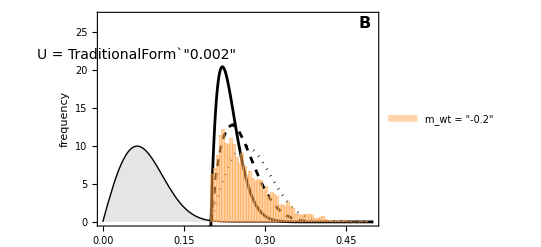

4136

```mathematica
dat1=Import[datadir<>"dfe_poisson_N10000_n4_c0.10_Es0.01_mmax0.50_mwt-0.20_mutmax10_nreps10000.csv"];
dat2=Import[datadir<>"dfe_poisson_N10000_n4_c0.10_Es0.01_mmax0.50_mwt-0.20_mutmax10_nreps100000.csv"];
dat={dat1,dat2};
mwtchoice=2;
params={n->4,Es->0.01, mmax->0.5,c->0.1};
nint=0.01;
letter=Style["B",16,Bold];

allmwts={-0.3,-0.2,-0.1};
mwts={allmwts[[mwtchoice]]};nmwts=Length[mwts];
legends=Table[Style[StringForm["m_wt = ``",NumberForm[mwts[[i]],3]],14],{i,nmwts}]; 
allcolors={Darker[Blue,0.7],Lighter[Orange],Red};
chartcolor={allcolors[[mwtchoice]]};
color=Directive[Black,Thickness[0.005]];(*colors*)
colordashed=Directive[Black,Dashed,Thickness[0.005]];(*colors*)
colordotted=Directive[Black,Dotted,Thickness[0.005]];(*colors*)
styl={FontFamily->"Times",FontSize->14};
mutlab=Style[StringForm["U = ``",NumberForm[c n^2 λ/4/.λ->2Es/n/.params,1]],14];

(ⅇ^((m-mmax)/α) (1-ⅇ^(-2 m)) (-m+mmax)^(-1+β) α^-β)/(Gamma[β] (1+(ⅇ^(-2 mmax) (1-2 α)^-β (-Gamma[β]+Gamma[β,mmax (-2+1/α)]))/Gamma[β]-Gamma[β,mmax/α]/Gamma[β]))/.α->λ (1+2ϵ)/(1+ϵ)/.β->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax-mwt/.λ->2Es/n/.params;
theory0step=Plot[%/.m->s+mwt/.mwt->0,{s,0,mmax/.params},PlotStyle->Black,PlotRange->All,Filling->Bottom,FillingStyle->{Black,Opacity[0.1]}];
(ⅇ^((m-mmax)/α) (1-ⅇ^(-2 m)) (-m+mmax)^(-1+β) α^-β)/(Gamma[β] (1+(ⅇ^(-2 mmax) (1-2 α)^-β (-Gamma[β]+Gamma[β,mmax (-2+1/α)]))/Gamma[β]-Gamma[β,mmax/α]/Gamma[β]))/.α->λ (1+2ϵ)/(1+ϵ)/.β->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax-mwt/.λ->2Es/n/.params;
theory1step=Plot[Table[%/.m->s+mwt/.mwt->mwts[[i]],{i,nmwts}],{s,0,mmax/.params},PlotStyle->color,PlotRange->All];

(ⅇ^((m2-mmax)/α) (1-ⅇ^(-2 m2)) (-m2+mmax)^(-1+β) α^-β)/(Gamma[β] (1+(ⅇ^(-2 mmax) (1-2 α)^-β (-Gamma[β]+Gamma[β,mmax (-2+1/α)]))/Gamma[β]-Gamma[β,mmax/α]/Gamma[β]))/.α->λ (1+2ϵ)/(1+ϵ)/.β->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax-Subscript[m, wt]/.Subscript[m, wt]->0/.λ->2Es/n/.params;
theory2stepcrit=Plot[Table[%/.m2->s+mwt/.mwt->mwts[[i]],{i,nmwts}],{s,0.1,mmax/.params},PlotStyle->colordotted,PlotRange->All,Axes->False];

mlim=-√(U (1+(-Gamma[Subscript[β, 0],mmax/Subscript[α, 0]]+ⅇ^(-2 mmax) Gamma[Subscript[β, 0],mmax (-2+1/Subscript[α, 0])] (1-2 Subscript[α, 0])^(-Subscript[β, 0]))/Gamma[Subscript[β, 0]]-ⅇ^(-2 mmax) (1-2 Subscript[α, 0])^(-Subscript[β, 0])))/.U->10^c Uc/.Uc->n^2 λ/4/.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params;
-(ⅇ^((m2-mmax)/Subscript[α, m1]+(m1-mmax)/Subscript[α, mwt]) (1-ⅇ^(-2 m2)) (-m1+mmax)^(-1+Subscript[β, mwt]) (-m2+mmax)^(-1+Subscript[β, m1]) Subscript[α, m1]^(-Subscript[β, m1]))/(m1 Gamma[Subscript[β, m1]])/.U->10^c Uc/.Uc->n^2 λ/4/.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params;
Table[
{m2-mwt/.mwt->mwts[[i]],NIntegrate[%/.mwt->mwts[[i]],{m1,-∞,mlim}]/NIntegrate[%/.mwt->mwts[[i]],{m1,-1,mlim},{m2,0,mmax/.params}]},
{i,nmwts},{m2,0.0001,0.2,nint}];
theory2stepsub=ListPlot[%,Joined->True,PlotRange->All,Axes->False,PlotStyle->colordashed];

dat//Flatten;
(*dat=Table[Max[dat[[i]]],{i,Length[dat]}];*)
data=Histogram[Table[%-mwt/.mwt->mwts[[i]],{i,nmwts}],50,"PDF",ChartStyle->chartcolor,ChartLegends->Placed[legends,Scaled@{0.175,0.9}]];

Show[
theory0step,theory1step,theory2stepcrit,theory2stepsub,data,
Frame->{True,True,False,False},
PlotRangePadding->None,
FrameLabel->{(*Style["mutant fitness effect, s=m-m_wt",16]*),Style["frequency",14]},
LabelStyle->styl,
PlotRange->{{0,0.5},{0,27}},
Epilog->{Text[mutlab,Scaled@{0.14,0.8}],Text[letter,Scaled@{0.95,0.95}]}
]

(*Export[imagedir<>"dfeMediumSmall.pdf",%];*)

Length[dat//Flatten]
```

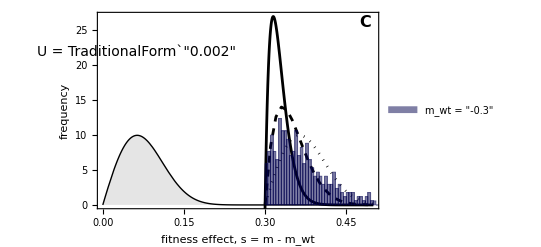

340

```mathematica
dat1=Import[datadir<>"dfe_poisson_N10000_n4_c0.10_Es0.01_mmax0.50_mwt-0.30_mutmax10_nreps100000.csv"];
dat2=Import[datadir<>"dfe_poisson_N10000_n4_c0.10_Es0.01_mmax0.50_mwt-0.30_mutmax10_nreps200000.csv"];
dat3=Import[datadir<>"dfe_poisson_N10000_n4_c0.10_Es0.01_mmax0.50_mwt-0.30_mutmax10_nreps200000b.csv"];
dat={dat1,dat2,dat3};
mwtchoice=1;
params={n->4,Es->0.01, mmax->0.5,c->0.1};
nint=0.01;
letter=Style["C",16,Bold];

allmwts={-0.3,-0.2,-0.1};
mwts={allmwts[[mwtchoice]]};nmwts=Length[mwts];
legends=Table[Style[StringForm["m_wt = ``",NumberForm[mwts[[i]],3]],14],{i,nmwts}]; 
allcolors={Darker[Blue,0.7],Lighter[Orange],Red};
chartcolor={allcolors[[mwtchoice]]};
color=Directive[Black,Thickness[0.005]];(*colors*)
colordashed=Directive[Black,Dashed,Thickness[0.005]];(*colors*)
colordotted=Directive[Black,Dotted,Thickness[0.005]];(*colors*)
styl={FontFamily->"Times",FontSize->14};
mutlab=Style[StringForm["U = ``",NumberForm[c n^2 λ/4/.λ->2Es/n/.params,1]],14];

(ⅇ^((m-mmax)/α) (1-ⅇ^(-2 m)) (-m+mmax)^(-1+β) α^-β)/(Gamma[β] (1+(ⅇ^(-2 mmax) (1-2 α)^-β (-Gamma[β]+Gamma[β,mmax (-2+1/α)]))/Gamma[β]-Gamma[β,mmax/α]/Gamma[β]))/.α->λ (1+2ϵ)/(1+ϵ)/.β->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax-mwt/.λ->2Es/n/.params;
theory0step=Plot[%/.m->s+mwt/.mwt->0,{s,0,mmax/.params},PlotStyle->Black,PlotRange->All,Filling->Bottom,FillingStyle->{Black,Opacity[0.1]}];
(ⅇ^((m-mmax)/α) (1-ⅇ^(-2 m)) (-m+mmax)^(-1+β) α^-β)/(Gamma[β] (1+(ⅇ^(-2 mmax) (1-2 α)^-β (-Gamma[β]+Gamma[β,mmax (-2+1/α)]))/Gamma[β]-Gamma[β,mmax/α]/Gamma[β]))/.α->λ (1+2ϵ)/(1+ϵ)/.β->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax-mwt/.λ->2Es/n/.params;
theory1step=Plot[Table[%/.m->s+mwt/.mwt->mwts[[i]],{i,nmwts}],{s,0,mmax/.params},PlotStyle->color,PlotRange->All];

(ⅇ^((m2-mmax)/α) (1-ⅇ^(-2 m2)) (-m2+mmax)^(-1+β) α^-β)/(Gamma[β] (1+(ⅇ^(-2 mmax) (1-2 α)^-β (-Gamma[β]+Gamma[β,mmax (-2+1/α)]))/Gamma[β]-Gamma[β,mmax/α]/Gamma[β]))/.α->λ (1+2ϵ)/(1+ϵ)/.β->n/2(1+ϵ)^2/(1+2ϵ)/.ϵ->2 so/(n λ)/.so->mmax-Subscript[m, wt]/.Subscript[m, wt]->0/.λ->2Es/n/.params;
theory2stepcrit=Plot[Table[%/.m2->s+mwt/.mwt->mwts[[i]],{i,nmwts}],{s,0.1,mmax/.params},PlotStyle->colordotted,PlotRange->All,Axes->False];

mlim=-√(U (1+(-Gamma[Subscript[β, 0],mmax/Subscript[α, 0]]+ⅇ^(-2 mmax) Gamma[Subscript[β, 0],mmax (-2+1/Subscript[α, 0])] (1-2 Subscript[α, 0])^(-Subscript[β, 0]))/Gamma[Subscript[β, 0]]-ⅇ^(-2 mmax) (1-2 Subscript[α, 0])^(-Subscript[β, 0])))/.U->10^c Uc/.Uc->n^2 λ/4/.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params;
-(ⅇ^((m2-mmax)/Subscript[α, m1]+(m1-mmax)/Subscript[α, mwt]) (1-ⅇ^(-2 m2)) (-m1+mmax)^(-1+Subscript[β, mwt]) (-m2+mmax)^(-1+Subscript[β, m1]) Subscript[α, m1]^(-Subscript[β, m1]))/(m1 Gamma[Subscript[β, m1]])/.U->10^c Uc/.Uc->n^2 λ/4/.Subscript[α, x_]->λ (1+2 Subscript[ϵ, x])/(1+Subscript[ϵ, x])/.Subscript[β, x_]->n/2(1+Subscript[ϵ, x])^2/(1+2 Subscript[ϵ, x])/.Subscript[ϵ, x_]->2 Subscript[so, x]/(n λ)/.Subscript[so, x_]->mmax-x/.λ->2Es/n/.params;
Table[
{m2-mwt/.mwt->mwts[[i]],NIntegrate[%/.mwt->mwts[[i]],{m1,-∞,mlim}]/NIntegrate[%/.mwt->mwts[[i]],{m1,-1,mlim},{m2,0,mmax/.params}]},
{i,nmwts},{m2,0.0001,0.2,nint}];
theory2stepsub=ListPlot[%,Joined->True,PlotRange->All,Axes->False,PlotStyle->colordashed];

dat//Flatten;
(*Table[Max[%[[i]]],{i,Length[%]}];*)
data=Histogram[Table[%-mwt/.mwt->mwts[[i]],{i,nmwts}],50,"PDF",ChartStyle->chartcolor,ChartLegends->Placed[legends,Scaled@{0.175,0.9}]];

Show[
theory0step,theory1step,theory2stepcrit,theory2stepsub,data,
Frame->{True,True,False,False},
PlotRangePadding->None,
FrameLabel->{Style["fitness effect, s = m - m_wt",14],Style["frequency",14]},
LabelStyle->styl,
PlotRange->{{0,0.5},{0,27}},
Epilog->{Text[mutlab,Scaled@{0.14,0.8}],Text[letter,Scaled@{0.95,0.95}]}
]

(*Export[imagedir<>"dfeFarSmall.pdf",%];*)

Length[dat//Flatten]
```